## The RGB Cube corners.

```mathematica
AppendTo[$Path, NotebookDirectory[]];
<<ColorSpacePackage`
```

```mathematica
Manipulate[ShowYABCube3D[θ,PlotRange-> {{0,√3/2},{-√(2/3) Cos[π/6-Mod[-π/6+θ,π/3]],√(2/3) Cos[π/6-Mod[-π/6+θ,π/3]]},{-√(2/3) Cos[π/6-Mod[θ,π/3]],√(2/3) Cos[π/6-Mod[θ,π/3]]}},ViewPoint->{10,0,0}],{θ,0,Pi}]
```

```mathematica
Manipulate[ShowYABCube3D[θ],{θ,0,Pi}]
```

```mathematica
Graphics3D[YABCubeFinite3D[0,8],GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
Graphics3D[Flatten[{EdgeForm[],Opacity[.7],YABCubeFinite3D[0,8]}],GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
Graphics3D[RGBCubeInYabFiniteBalls[0,3,8],GraphicsCubeOpts]
```

```mathematica
Graphics3D[RGBCubeInYabFiniteBalls[0,3,8,{0.8,0.01}],GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
Graphics3D[Flatten[{EdgeForm[],Opacity[.7],RGBCubeFinite3D[8]}],GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
YABColorFast[0.5,0.4,0.9]
```

-Graphics-

```mathematica
n=8;Graphics3D[{Opacity[.7],Raster3D[Table[YABColorFastList[k,j,i],{i,0,1,1/n},{j,0,1,1/n},{k,0,1,1/n}],ColorFunction->Hue]},GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
n=2^8/2^3;
Graphics3D[{Opacity[.7],Raster3D[Table[YABColorFastList[k,j,i],{i,0,1,1/n},{j,0,1,1/n},{k,0,1,1/n}],ColorFunction->Hue]},GraphicsCubeOpts]
```

-Graphics3D-

```mathematica
n=8;Raster3D[Table[List[r,g,b],{b,0,1,1/n},{g,0,1,1/n},{r,0,1,1/n}],{{0,0,0},{1,1,1}},ColorFunction->RGBColor]
```

Raster3D[{{{{0,0,0},{1/8,0,0},{1/4,0,0},{3/8,0,0},{1/2,0,0},{5/8,0,0},{3/4,0,0},{7/8,0,0},{1,0,0}},{{0,1/8,0},{1/8,1/8,0},{1/4,1/8,0},{3/8,1/8,0},{1/2,1/8,0},{5/8,1/8,0},{3/4,1/8,0},{7/8,1/8,0},{1,1/8,0}},{{0,1/4,0},{1/8,1/4,0},{1/4,1/4,0},{3/8,1/4,0},{1/2,1/4,0},{5/8,1/4,0},{3/4,1/4,0},{7/8,1/4,0},{1,1/4,0}},{{0,3/8,0},{1/8,3/8,0},{1/4,3/8,0},{3/8,3/8,0},{1/2,3/8,0},{5/8,3/8,0},{3/4,3/8,0},{7/8,3/8,0},{1,3/8,0}},{{0,1/2,0},{1/8,1/2,0},{1/4,1/2,0},{3/8,1/2,0},{1/2,1/2,0},{5/8,1/2,0},{3/4,1/2,0},{7/8,1/2,0},{1,1/2,0}},{{0,5/8,0},{1/8,5/8,0},{1/4,5/8,0},{3/8,5/8,0},{1/2,5/8,0},{5/8,5/8,0},{3/4,5/8,0},{7/8,5/8,0},{1,5/8,0}},{{0,3/4,0},{1/8,3/4,0},{1/4,3/4,0},{3/8,3/4,0},{1/2,3/4,0},{5/8,3/4,0},{3/4,3/4,0},{7/8,3/4,0},{1,3/4,0}},{{0,7/8,0},{1/8,7/8,0},{1/4,7/8,0},{3/8,7/8,0},{1/2,7/8,0},{5/8,7/8,0},{3/4,7/8,0},{7/8,7/8,0},{1,7/8,0}},{{0,1,0},{1/8,1,0},{1/4,1,0},{3/8,1,0},{1/2,1,0},{5/8,1,0},{3/4,1,0},{7/8,1,0},{1,1,0}}},{{{0,0,1/8},{1/8,0,1/8},{1/4,0,1/8},{3/8,0,1/8},{1/2,0,1/8},{5/8,0,1/8},{3/4,0,1/8},{7/8,0,1/8},{1,0,1/8}},{{0,1/8,1/8},{1/8,1/8,1/8},{1/4,1/8,1/8},{3/8,1/8,1/8},{1/2,1/8,1/8},{5/8,1/8,1/8},{3/4,1/8,1/8},{7/8,1/8,1/8},{1,1/8,1/8}},{{0,1/4,1/8},{1/8,1/4,1/8},{1/4,1/4,1/8},{3/8,1/4,1/8},{1/2,1/4,1/8},{5/8,1/4,1/8},{3/4,1/4,1/8},{7/8,1/4,1/8},{1,1/4,1/8}},{{0,3/8,1/8},{1/8,3/8,1/8},{1/4,3/8,1/8},{3/8,3/8,1/8},{1/2,3/8,1/8},{5/8,3/8,1/8},{3/4,3/8,1/8},{7/8,3/8,1/8},{1,3/8,1/8}},{{0,1/2,1/8},{1/8,1/2,1/8},{1/4,1/2,1/8},{3/8,1/2,1/8},{1/2,1/2,1/8},{5/8,1/2,1/8},{3/4,1/2,1/8},{7/8,1/2,1/8},{1,1/2,1/8}},{{0,5/8,1/8},{1/8,5/8,1/8},{1/4,5/8,1/8},{3/8,5/8,1/8},{1/2,5/8,1/8},{5/8,5/8,1/8},{3/4,5/8,1/8},{7/8,5/8,1/8},{1,5/8,1/8}},{{0,3/4,1/8},{1/8,3/4,1/8},{1/4,3/4,1/8},{3/8,3/4,1/8},{1/2,3/4,1/8},{5/8,3/4,1/8},{3/4,3/4,1/8},{7/8,3/4,1/8},{1,3/4,1/8}},{{0,7/8,1/8},{1/8,7/8,1/8},{1/4,7/8,1/8},{3/8,7/8,1/8},{1/2,7/8,1/8},{5/8,7/8,1/8},{3/4,7/8,1/8},{7/8,7/8,1/8},{1,7/8,1/8}},{{0,1,1/8},{1/8,1,1/8},{1/4,1,1/8},{3/8,1,1/8},{1/2,1,1/8},{5/8,1,1/8},{3/4,1,1/8},{7/8,1,1/8},{1,1,1/8}}},{{{0,0,1/4},{1/8,0,1/4},{1/4,0,1/4},{3/8,0,1/4},{1/2,0,1/4},{5/8,0,1/4},{3/4,0,1/4},{7/8,0,1/4},{1,0,1/4}},{{0,1/8,1/4},{1/8,1/8,1/4},{1/4,1/8,1/4},{3/8,1/8,1/4},{1/2,1/8,1/4},{5/8,1/8,1/4},{3/4,1/8,1/4},{7/8,1/8,1/4},{1,1/8,1/4}},{{0,1/4,1/4},{1/8,1/4,1/4},{1/4,1/4,1/4},{3/8,1/4,1/4},{1/2,1/4,1/4},{5/8,1/4,1/4},{3/4,1/4,1/4},{7/8,1/4,1/4},{1,1/4,1/4}},{{0,3/8,1/4},{1/8,3/8,1/4},{1/4,3/8,1/4},{3/8,3/8,1/4},{1/2,3/8,1/4},{5/8,3/8,1/4},{3/4,3/8,1/4},{7/8,3/8,1/4},{1,3/8,1/4}},{{0,1/2,1/4},{1/8,1/2,1/4},{1/4,1/2,1/4},{3/8,1/2,1/4},{1/2,1/2,1/4},{5/8,1/2,1/4},{3/4,1/2,1/4},{7/8,1/2,1/4},{1,1/2,1/4}},{{0,5/8,1/4},{1/8,5/8,1/4},{1/4,5/8,1/4},{3/8,5/8,1/4},{1/2,5/8,1/4},{5/8,5/8,1/4},{3/4,5/8,1/4},{7/8,5/8,1/4},{1,5/8,1/4}},{{0,3/4,1/4},{1/8,3/4,1/4},{1/4,3/4,1/4},{3/8,3/4,1/4},{1/2,3/4,1/4},{5/8,3/4,1/4},{3/4,3/4,1/4},{7/8,3/4,1/4},{1,3/4,1/4}},{{0,7/8,1/4},{1/8,7/8,1/4},{1/4,7/8,1/4},{3/8,7/8,1/4},{1/2,7/8,1/4},{5/8,7/8,1/4},{3/4,7/8,1/4},{7/8,7/8,1/4},{1,7/8,1/4}},{{0,1,1/4},{1/8,1,1/4},{1/4,1,1/4},{3/8,1,1/4},{1/2,1,1/4},{5/8,1,1/4},{3/4,1,1/4},{7/8,1,1/4},{1,1,1/4}}},{{{0,0,3/8},{1/8,0,3/8},{1/4,0,3/8},{3/8,0,3/8},{1/2,0,3/8},{5/8,0,3/8},{3/4,0,3/8},{7/8,0,3/8},{1,0,3/8}},{{0,1/8,3/8},{1/8,1/8,3/8},{1/4,1/8,3/8},{3/8,1/8,3/8},{1/2,1/8,3/8},{5/8,1/8,3/8},{3/4,1/8,3/8},{7/8,1/8,3/8},{1,1/8,3/8}},{{0,1/4,3/8},{1/8,1/4,3/8},{1/4,1/4,3/8},{3/8,1/4,3/8},{1/2,1/4,3/8},{5/8,1/4,3/8},{3/4,1/4,3/8},{7/8,1/4,3/8},{1,1/4,3/8}},{{0,3/8,3/8},{1/8,3/8,3/8},{1/4,3/8,3/8},{3/8,3/8,3/8},{1/2,3/8,3/8},{5/8,3/8,3/8},{3/4,3/8,3/8},{7/8,3/8,3/8},{1,3/8,3/8}},{{0,1/2,3/8},{1/8,1/2,3/8},{1/4,1/2,3/8},{3/8,1/2,3/8},{1/2,1/2,3/8},{5/8,1/2,3/8},{3/4,1/2,3/8},{7/8,1/2,3/8},{1,1/2,3/8}},{{0,5/8,3/8},{1/8,5/8,3/8},{1/4,5/8,3/8},{3/8,5/8,3/8},{1/2,5/8,3/8},{5/8,5/8,3/8},{3/4,5/8,3/8},{7/8,5/8,3/8},{1,5/8,3/8}},{{0,3/4,3/8},{1/8,3/4,3/8},{1/4,3/4,3/8},{3/8,3/4,3/8},{1/2,3/4,3/8},{5/8,3/4,3/8},{3/4,3/4,3/8},{7/8,3/4,3/8},{1,3/4,3/8}},{{0,7/8,3/8},{1/8,7/8,3/8},{1/4,7/8,3/8},{3/8,7/8,3/8},{1/2,7/8,3/8},{5/8,7/8,3/8},{3/4,7/8,3/8},{7/8,7/8,3/8},{1,7/8,3/8}},{{0,1,3/8},{1/8,1,3/8},{1/4,1,3/8},{3/8,1,3/8},{1/2,1,3/8},{5/8,1,3/8},{3/4,1,3/8},{7/8,1,3/8},{1,1,3/8}}},{{{0,0,1/2},{1/8,0,1/2},{1/4,0,1/2},{3/8,0,1/2},{1/2,0,1/2},{5/8,0,1/2},{3/4,0,1/2},{7/8,0,1/2},{1,0,1/2}},{{0,1/8,1/2},{1/8,1/8,1/2},{1/4,1/8,1/2},{3/8,1/8,1/2},{1/2,1/8,1/2},{5/8,1/8,1/2},{3/4,1/8,1/2},{7/8,1/8,1/2},{1,1/8,1/2}},{{0,1/4,1/2},{1/8,1/4,1/2},{1/4,1/4,1/2},{3/8,1/4,1/2},{1/2,1/4,1/2},{5/8,1/4,1/2},{3/4,1/4,1/2},{7/8,1/4,1/2},{1,1/4,1/2}},{{0,3/8,1/2},{1/8,3/8,1/2},{1/4,3/8,1/2},{3/8,3/8,1/2},{1/2,3/8,1/2},{5/8,3/8,1/2},{3/4,3/8,1/2},{7/8,3/8,1/2},{1,3/8,1/2}},{{0,1/2,1/2},{1/8,1/2,1/2},{1/4,1/2,1/2},{3/8,1/2,1/2},{1/2,1/2,1/2},{5/8,1/2,1/2},{3/4,1/2,1/2},{7/8,1/2,1/2},{1,1/2,1/2}},{{0,5/8,1/2},{1/8,5/8,1/2},{1/4,5/8,1/2},{3/8,5/8,1/2},{1/2,5/8,1/2},{5/8,5/8,1/2},{3/4,5/8,1/2},{7/8,5/8,1/2},{1,5/8,1/2}},{{0,3/4,1/2},{1/8,3/4,1/2},{1/4,3/4,1/2},{3/8,3/4,1/2},{1/2,3/4,1/2},{5/8,3/4,1/2},{3/4,3/4,1/2},{7/8,3/4,1/2},{1,3/4,1/2}},{{0,7/8,1/2},{1/8,7/8,1/2},{1/4,7/8,1/2},{3/8,7/8,1/2},{1/2,7/8,1/2},{5/8,7/8,1/2},{3/4,7/8,1/2},{7/8,7/8,1/2},{1,7/8,1/2}},{{0,1,1/2},{1/8,1,1/2},{1/4,1,1/2},{3/8,1,1/2},{1/2,1,1/2},{5/8,1,1/2},{3/4,1,1/2},{7/8,1,1/2},{1,1,1/2}}},{{{0,0,5/8},{1/8,0,5/8},{1/4,0,5/8},{3/8,0,5/8},{1/2,0,5/8},{5/8,0,5/8},{3/4,0,5/8},{7/8,0,5/8},{1,0,5/8}},{{0,1/8,5/8},{1/8,1/8,5/8},{1/4,1/8,5/8},{3/8,1/8,5/8},{1/2,1/8,5/8},{5/8,1/8,5/8},{3/4,1/8,5/8},{7/8,1/8,5/8},{1,1/8,5/8}},{{0,1/4,5/8},{1/8,1/4,5/8},{1/4,1/4,5/8},{3/8,1/4,5/8},{1/2,1/4,5/8},{5/8,1/4,5/8},{3/4,1/4,5/8},{7/8,1/4,5/8},{1,1/4,5/8}},{{0,3/8,5/8},{1/8,3/8,5/8},{1/4,3/8,5/8},{3/8,3/8,5/8},{1/2,3/8,5/8},{5/8,3/8,5/8},{3/4,3/8,5/8},{7/8,3/8,5/8},{1,3/8,5/8}},{{0,1/2,5/8},{1/8,1/2,5/8},{1/4,1/2,5/8},{3/8,1/2,5/8},{1/2,1/2,5/8},{5/8,1/2,5/8},{3/4,1/2,5/8},{7/8,1/2,5/8},{1,1/2,5/8}},{{0,5/8,5/8},{1/8,5/8,5/8},{1/4,5/8,5/8},{3/8,5/8,5/8},{1/2,5/8,5/8},{5/8,5/8,5/8},{3/4,5/8,5/8},{7/8,5/8,5/8},{1,5/8,5/8}},{{0,3/4,5/8},{1/8,3/4,5/8},{1/4,3/4,5/8},{3/8,3/4,5/8},{1/2,3/4,5/8},{5/8,3/4,5/8},{3/4,3/4,5/8},{7/8,3/4,5/8},{1,3/4,5/8}},{{0,7/8,5/8},{1/8,7/8,5/8},{1/4,7/8,5/8},{3/8,7/8,5/8},{1/2,7/8,5/8},{5/8,7/8,5/8},{3/4,7/8,5/8},{7/8,7/8,5/8},{1,7/8,5/8}},{{0,1,5/8},{1/8,1,5/8},{1/4,1,5/8},{3/8,1,5/8},{1/2,1,5/8},{5/8,1,5/8},{3/4,1,5/8},{7/8,1,5/8},{1,1,5/8}}},{{{0,0,3/4},{1/8,0,3/4},{1/4,0,3/4},{3/8,0,3/4},{1/2,0,3/4},{5/8,0,3/4},{3/4,0,3/4},{7/8,0,3/4},{1,0,3/4}},{{0,1/8,3/4},{1/8,1/8,3/4},{1/4,1/8,3/4},{3/8,1/8,3/4},{1/2,1/8,3/4},{5/8,1/8,3/4},{3/4,1/8,3/4},{7/8,1/8,3/4},{1,1/8,3/4}},{{0,1/4,3/4},{1/8,1/4,3/4},{1/4,1/4,3/4},{3/8,1/4,3/4},{1/2,1/4,3/4},{5/8,1/4,3/4},{3/4,1/4,3/4},{7/8,1/4,3/4},{1,1/4,3/4}},{{0,3/8,3/4},{1/8,3/8,3/4},{1/4,3/8,3/4},{3/8,3/8,3/4},{1/2,3/8,3/4},{5/8,3/8,3/4},{3/4,3/8,3/4},{7/8,3/8,3/4},{1,3/8,3/4}},{{0,1/2,3/4},{1/8,1/2,3/4},{1/4,1/2,3/4},{3/8,1/2,3/4},{1/2,1/2,3/4},{5/8,1/2,3/4},{3/4,1/2,3/4},{7/8,1/2,3/4},{1,1/2,3/4}},{{0,5/8,3/4},{1/8,5/8,3/4},{1/4,5/8,3/4},{3/8,5/8,3/4},{1/2,5/8,3/4},{5/8,5/8,3/4},{3/4,5/8,3/4},{7/8,5/8,3/4},{1,5/8,3/4}},{{0,3/4,3/4},{1/8,3/4,3/4},{1/4,3/4,3/4},{3/8,3/4,3/4},{1/2,3/4,3/4},{5/8,3/4,3/4},{3/4,3/4,3/4},{7/8,3/4,3/4},{1,3/4,3/4}},{{0,7/8,3/4},{1/8,7/8,3/4},{1/4,7/8,3/4},{3/8,7/8,3/4},{1/2,7/8,3/4},{5/8,7/8,3/4},{3/4,7/8,3/4},{7/8,7/8,3/4},{1,7/8,3/4}},{{0,1,3/4},{1/8,1,3/4},{1/4,1,3/4},{3/8,1,3/4},{1/2,1,3/4},{5/8,1,3/4},{3/4,1,3/4},{7/8,1,3/4},{1,1,3/4}}},{{{0,0,7/8},{1/8,0,7/8},{1/4,0,7/8},{3/8,0,7/8},{1/2,0,7/8},{5/8,0,7/8},{3/4,0,7/8},{7/8,0,7/8},{1,0,7/8}},{{0,1/8,7/8},{1/8,1/8,7/8},{1/4,1/8,7/8},{3/8,1/8,7/8},{1/2,1/8,7/8},{5/8,1/8,7/8},{3/4,1/8,7/8},{7/8,1/8,7/8},{1,1/8,7/8}},{{0,1/4,7/8},{1/8,1/4,7/8},{1/4,1/4,7/8},{3/8,1/4,7/8},{1/2,1/4,7/8},{5/8,1/4,7/8},{3/4,1/4,7/8},{7/8,1/4,7/8},{1,1/4,7/8}},{{0,3/8,7/8},{1/8,3/8,7/8},{1/4,3/8,7/8},{3/8,3/8,7/8},{1/2,3/8,7/8},{5/8,3/8,7/8},{3/4,3/8,7/8},{7/8,3/8,7/8},{1,3/8,7/8}},{{0,1/2,7/8},{1/8,1/2,7/8},{1/4,1/2,7/8},{3/8,1/2,7/8},{1/2,1/2,7/8},{5/8,1/2,7/8},{3/4,1/2,7/8},{7/8,1/2,7/8},{1,1/2,7/8}},{{0,5/8,7/8},{1/8,5/8,7/8},{1/4,5/8,7/8},{3/8,5/8,7/8},{1/2,5/8,7/8},{5/8,5/8,7/8},{3/4,5/8,7/8},{7/8,5/8,7/8},{1,5/8,7/8}},{{0,3/4,7/8},{1/8,3/4,7/8},{1/4,3/4,7/8},{3/8,3/4,7/8},{1/2,3/4,7/8},{5/8,3/4,7/8},{3/4,3/4,7/8},{7/8,3/4,7/8},{1,3/4,7/8}},{{0,7/8,7/8},{1/8,7/8,7/8},{1/4,7/8,7/8},{3/8,7/8,7/8},{1/2,7/8,7/8},{5/8,7/8,7/8},{3/4,7/8,7/8},{7/8,7/8,7/8},{1,7/8,7/8}},{{0,1,7/8},{1/8,1,7/8},{1/4,1,7/8},{3/8,1,7/8},{1/2,1,7/8},{5/8,1,7/8},{3/4,1,7/8},{7/8,1,7/8},{1,1,7/8}}},{{{0,0,1},{1/8,0,1},{1/4,0,1},{3/8,0,1},{1/2,0,1},{5/8,0,1},{3/4,0,1},{7/8,0,1},{1,0,1}},{{0,1/8,1},{1/8,1/8,1},{1/4,1/8,1},{3/8,1/8,1},{1/2,1/8,1},{5/8,1/8,1},{3/4,1/8,1},{7/8,1/8,1},{1,1/8,1}},{{0,1/4,1},{1/8,1/4,1},{1/4,1/4,1},{3/8,1/4,1},{1/2,1/4,1},{5/8,1/4,1},{3/4,1/4,1},{7/8,1/4,1},{1,1/4,1}},{{0,3/8,1},{1/8,3/8,1},{1/4,3/8,1},{3/8,3/8,1},{1/2,3/8,1},{5/8,3/8,1},{3/4,3/8,1},{7/8,3/8,1},{1,3/8,1}},{{0,1/2,1},{1/8,1/2,1},{1/4,1/2,1},{3/8,1/2,1},{1/2,1/2,1},{5/8,1/2,1},{3/4,1/2,1},{7/8,1/2,1},{1,1/2,1}},{{0,5/8,1},{1/8,5/8,1},{1/4,5/8,1},{3/8,5/8,1},{1/2,5/8,1},{5/8,5/8,1},{3/4,5/8,1},{7/8,5/8,1},{1,5/8,1}},{{0,3/4,1},{1/8,3/4,1},{1/4,3/4,1},{3/8,3/4,1},{1/2,3/4,1},{5/8,3/4,1},{3/4,3/4,1},{7/8,3/4,1},{1,3/4,1}},{{0,7/8,1},{1/8,7/8,1},{1/4,7/8,1},{3/8,7/8,1},{1/2,7/8,1},{5/8,7/8,1},{3/4,7/8,1},{7/8,7/8,1},{1,7/8,1}},{{0,1,1},{1/8,1,1},{1/4,1,1},{3/8,1,1},{1/2,1,1},{5/8,1,1},{3/4,1,1},{7/8,1,1},{1,1,1}}}},{{0,0,0},{1,1,1}},ColorFunction→RGBColor]

```mathematica
Graphics3D[cube]
```

-Graphics3D-

```mathematica
Graphics3D[cube,GraphicsCubeOptions[Axes->True,AxesLabel->{"Blue","Green","Red"}]]
```

-Graphics3D-

```mathematica
cube=RGBCubeFinite3D[8];

GraphicsGrid[{{Graphics3D[cube,Axes->True,AxesLabel->{"Red","Green","Blue"},GraphicsCubeOpts],
Graphics3D[Rotate[cube,Pi/4,{0,1,0}],Axes->True,AxesLabel->{"Red","Green","Chrom B"},GraphicsCubeOpts],
Graphics3D[Rotate[Rotate[cube,Pi/4,{0,1,0}],-ArcTan[1/Sqrt[2]],{0,0,1}],Axes->True,GraphicsCubeOpts],Graphics3D[Rotate[Rotate[Rotate[cube,Pi/4,{0,1,0}],-ArcTan[1/Sqrt[2]],{0,0,1}],Pi/4,{1,0,0}],Axes->True,GraphicsCubeOpts]}}]
```

-Graphics-

```mathematica
Graphics3D[{Opacity[.7],RGBCubeInYabFinite[θ,3]},GraphicsCubeOptions[ViewPoint->{Infinity,0,0}]]/.θ->0
```

-Graphics3D-

## Rotation Matrices

Any 3 D rotation can be expressed as the product of 3 rotations about the cartesian axis.

```mathematica
Row[{MatrixForm[RotationMatrixX[α]],".",MatrixForm[RotationMatrixZ[γ]],".",MatrixForm[RotationMatrixY[β]]," =",MatrixForm[R[α,β, γ]]}]
```

(1 | 0 | 0
0 | Cos[α] | Sin[α]
0 | -Sin[α] | Cos[α]).(Cos[γ] | Sin[γ] | 0
-Sin[γ] | Cos[γ] | 0
0 | 0 | 1).(Cos[β] | 0 | -Sin[β]
0 | 1 | 0
Sin[β] | 0 | Cos[β]) =(1/2 (Cos[β-γ]+Cos[β+γ]) | Sin[γ] | 1/2 (-Sin[β-γ]-Sin[β+γ])
1/4 (2 Cos[α-β]-2 Cos[α+β]+Sin[α-β-γ]+Sin[α+β-γ]-Sin[α-β+γ]-Sin[α+β+γ]) | 1/2 (Cos[α-γ]+Cos[α+γ]) | 1/4 (-Cos[α-β-γ]+Cos[α+β-γ]+Cos[α-β+γ]-Cos[α+β+γ]+2 Sin[α-β]+2 Sin[α+β])
1/4 (Cos[α-β-γ]+Cos[α+β-γ]-Cos[α-β+γ]-Cos[α+β+γ]-2 Sin[α-β]+2 Sin[α+β]) | 1/2 (-Sin[α-γ]-Sin[α+γ]) | 1/4 (2 Cos[α-β]+2 Cos[α+β]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ]))

Solution for the Yab cube. Luminocity axis is in the X value.

```mathematica
Print[MatrixForm[YAB[θ]].MatrixForm[RGBCube],"=",MatrixForm[Map[TrigFactor,FullSimplify[TrigFactor[YAB[θ]. RGBCube]]],1]]
Print[MatrixForm[iYAB[θ]].MatrixForm[RGBCube["YAB"][θ]],"=",MatrixForm[Map[TrigFactor,FullSimplify[TrigFactor[iYAB[θ]. RGBCube["YAB"][θ]]]],1]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ]).(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)=(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)

(1/(√3) | -√(2/3) Sin[π/6+θ] | -√(2/3) Cos[π/6+θ]
1/(√3) | √(2/3) Cos[θ] | -√(2/3) Sin[θ]
1/(√3) | -√(2/3) Sin[π/6-θ] | √(2/3) Cos[π/6-θ]).(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)=(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

The inverse of a rotation is equal to the transpose of the rotation matrix

```mathematica
TrigFactor[FullSimplify[TrigToExp[Inverse[YAB[θ]]]]] == Transpose[YAB[θ]]
```

True

#### Cube Corners

To get the corners of the RGBCube in RGB and YAB space we can use

```mathematica
Row[{"RGBCube"["RGB"]," = ", MatrixForm[RGBCube["RGB"]],"    ","RGBCube"["YAB"][0]," = ", MatrixForm[RGBCube["YAB"][0]]}]
```

RGBCube[RGB] = (0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)    RGBCube[YAB][0] = (0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -1/(√6) | 1/(√6) | √(2/3) | 1/(√6) | -1/(√6) | -√(2/3) | 0
0 | -1/(√2) | -1/(√2) | 0 | 1/(√2) | 1/(√2) | 0 | 0)

To get the corners of the YabCube in RGB and YAB space we can use

```mathematica
Row[{"YABCube"["RGB"][0]," = ", MatrixForm[YABCube["RGB"][0]],"    ","YABCube"["YAB"][0]," = ", MatrixForm[YABCube["YAB"][0]]}]
```

YABCube[RGB][0] = (5/6 | 11/6 | 7/6 | 1/6 | -5/6 | -1/6 | 5/6 | 1/6
-2/3 | 1/3 | 5/3 | 2/3 | 2/3 | -2/3 | 1/3 | 5/3
-1/6 | 5/6 | 1/6 | -5/6 | 1/6 | 5/6 | 11/6 | 7/6)    YABCube[YAB][0] = (0 | √3 | √3 | 0 | 0 | 0 | √3 | √3
-√(2/3) | -√(2/3) | √(2/3) | √(2/3) | √(2/3) | -√(2/3) | -√(2/3) | √(2/3)
-1/(√2) | -1/(√2) | -1/(√2) | -1/(√2) | 1/(√2) | 1/(√2) | 1/(√2) | 1/(√2))

#### Axis Ranges

Functionally the axis ranges for the Yab axis are given by

```mathematica
Row[{"YABAxisRanges"[θ]," = ",MatrixForm[YABAxisRanges[θ]]}]
```

YABAxisRanges[θ] = (0 | √3
-√(2/3) Cos[π/6-Mod[-π/6+θ,π/3]] | √(2/3) Cos[π/6-Mod[-π/6+θ,π/3]]
-√(2/3) Cos[π/6-Mod[θ,π/3]] | √(2/3) Cos[π/6-Mod[θ,π/3]])

```mathematica
Manipulate[Block[{maxRanges,ranges, cube},
maxRanges = {{0,√3},{-√(2/3),√(2/3)},{-√(2/3),√(2/3)}};
ranges = YABAxisRanges[θ];
cube = Cuboid[{{ranges[[1,1]],ranges[[2,1]],ranges[[3,1]]},{ranges[[1,2]],ranges[[2,2]],ranges[[3,2]]}}];
Grid[{{Show[
Graphics[Raster[Table[Table[inYAB[θ].{Y,a,b},{a,-0.5,0.5,0.02}],{b,-0.5,0.5,0.02}]]]
,ImageSize->400],Graphics[{Black,Rectangle[Sequence@@Transpose[{YABAxisRanges[θ ][[2]],YABAxisRanges[θ ][[3]]}]],Blue,Polygon[YABPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube["RGB"]][[{2,3,4,5,6,7}]]]]]},PlotRange->{maxRanges[[2]],maxRanges[[3]]},ImageSize->400]}}]
],{θ,0,Pi},{{Y,0.5},0,1}]
```

```mathematica
Clear[theta]
```

```mathematica
cube3D=Flatten[{Opacity[1],RGBCubeInYabFinite[0,Sqrt[3]],YABAxisEnds3D[0,3]}]
```

Table::iterb: Iterator {k, 0, 1, 1/n} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

{Opacity[1],Raster3D[Table[{i,j,k,If[i+j+k<√3,1,0.03]},{k,0,1,1/n},{j,0,1,1/n},{i,0,1,1/n}],{{0,0,0},{1,1,1}},ColorFunction→RGBColor],Glow[-Graphics-],-Graphics-,Cylinder[{{0,0,0},{0.001,0,0}},0.1],Glow[-Graphics-],-Graphics-,Cylinder[{{√3,0,0},{1.73105,0,0}},0.1],Glow[Hue[0.833333,0.707107,3/2]],-Graphics-,Cylinder[{{(√3)/2,-√(2/3),0},{(√3)/2,-0.815497,0}},0.1],Glow[Hue[0.333333,0.707107,3/2]],-Graphics-,Cylinder[{{(√3)/2,√(2/3),0},{(√3)/2,0.815497,0}},0.1],Glow[Hue[0.0833333,0.707107,3/2]],-Graphics-,Cylinder[{{(√3)/2,0,-1/(√2)},{(√3)/2,0,-0.706107}},0.1],Glow[Hue[0.583333,0.707107,3/2]],-Graphics-,Cylinder[{{(√3)/2,0,1/(√2)},{(√3)/2,0,0.706107}},0.1]}

```mathematica
Manipulate[Block[{maxRanges, ranges, cube, centersB, centersA, cols}, 
   MaxTheta = Pi/2+0.2;
maxRanges = {{0, Sqrt[3]}, {-Sqrt[2/3], Sqrt[2/3]}, {-Sqrt[2/3], Sqrt[2/3]}};
imgScale = 200;
ranges = YABAxisRanges[θ]; 
  cube = Cuboid[{{ranges[[1,1]], ranges[[2,1]], ranges[[3,1]]}, {ranges[[1,2]], ranges[[2,2]], ranges[[3,2]]}}]; 
  centersB = RGBCube["YAB"][θ][[3]];
centersA = RGBCube["YAB"][θ][[2]]; 
cols = MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]]]]; 
  ticks =Prepend[ Table[{N[i*(Pi/6)], i*(Pi/6)}, {i, 0, 6*(MaxTheta/Pi)}],{N[θ],"θ"}];
CbWidth  = maxRanges[[2,2]] - maxRanges[[2,1]] + MaxTheta; 
  CbHeight = maxRanges[[3,2]] - maxRanges[[3,1]];
Cb = Plot[Evaluate[RGBCube["YAB"][theta][[3]]], {theta, 0, MaxTheta}, 
         PlotStyle -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]]]], 
     FrameTicks -> {{All, None}, {None,ticks}}, 
         FrameLabel -> { {"RGB Cube corner position in Cb",None},{None,None}}, 
     PlotRange -> {{0, MaxTheta - maxRanges[[2,1]] + maxRanges[[2,2]]}, maxRanges[[3]]}, 
         Frame -> True, 
     Epilog -> Flatten[{Line[{{θ, -Sqrt[2/3]}, {θ, Sqrt[2/3]}}],
    {Opacity[0.8],  Table[{cols[[i]], Disk[{θ, centersB[[i]]}, 0.04]}, {i, 1, 8}]}, 
           {Black, Translate[Rectangle[Sequence @@ Transpose[{YABAxisRanges[θ][[2]], YABAxisRanges[θ][[3]]}]], {MaxTheta - maxRanges[[2,1]], 0}], 
            Blue, Translate[
          Polygon[YABPolygon[θ], VertexColors -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]][[{2, 3, 4, 5, 6, 7}]]]]],
          {MaxTheta - maxRanges[[2,1]], 0}]
   }}], 
  AspectRatio -> CbHeight/CbWidth, 
      ImageSize -> Floor[imgScale*{CbWidth, CaHeight}]
]; 
CaWidth = maxRanges[[3,2]] - maxRanges[[3,1]] + MaxTheta; 
  CaHeight = maxRanges[[2,2]] - maxRanges[[2,1]];
Ca = Plot[Evaluate[RGBCube["YAB"][theta][[2]]], {theta, 0, MaxTheta}, 
         PlotStyle -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]]]], 
     FrameTicks -> {{All, None}, {ticks, None}}, 
         FrameLabel -> {None, "RGB Cube corner position in Ca"}, 
     PlotRange -> {{0, MaxTheta - maxRanges[[3,1]] + maxRanges[[3,2]]}, maxRanges[[2]]}, 
         Frame -> True, 
     Epilog -> Flatten[{Line[{{θ, -Sqrt[2/3]}, {θ, Sqrt[2/3]}}], 
    {Opacity[0.8], Table[{cols[[i]], Disk[{θ, centersA[[i]]}, 0.04]}, {i, 1, 8}]}, 
           {Black, Translate[Rectangle[Sequence @@ Transpose[{YABAxisRanges[θ][[3]], YABAxisRanges[θ][[2]]}]], {MaxTheta - maxRanges[[3,1]], 0}], 
            Blue, Translate[Polygon[YABPolygon[θ - Pi/2], VertexColors -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]][[
                {2, 3, 4, 5, 6, 7}]]]]], {MaxTheta - maxRanges[[3,1]], 0}]}}], 
     AspectRatio -> CaHeight/CaWidth, 
         ImageSize -> Floor[imgScale*{CaWidth, CaHeight}]
   ]; 

opt=GraphicsCubeOptions[ PlotRange->YABAxisRanges[θ],ViewPoint->{8,5,-10},ImageSize->500];

cube3D=Flatten[{Opacity[1],RGBCubeInYabFinite[θ,cut],YABAxisEnds3D[θ,brighten]}];

    Column[{Graphics3D[cube3D,opt],Show[Graphics[{Inset[Cb, Floor[imgScale*{CbWidth, 0}], {CbWidth, maxRanges[[3,1]]}, Floor[imgScale*{CbWidth, CbHeight}]], 
       Inset[Ca, Floor[imgScale*{CaWidth, 0}], {CaWidth, maxRanges[[2,2]]}, Floor[imgScale*{CaWidth, CaHeight}], {0, -1}]}], 
     PlotRange -> Floor[imgScale*{{0, CbWidth}, {0, CaWidth}}],ImageSize->500]}]
]
, {θ, 0, MaxTheta},{brighten,1,2},{{cut,3},0,3}]
```

```mathematica
eq=Map[(0≤#≤1)&,iYAB[θ].{y,a,b}];
MatrixForm[eq]
```

(0≤y/(√3)-√(2/3) b Cos[π/6+θ]-√(2/3) a Sin[π/6+θ]≤1
0≤y/(√3)+√(2/3) a Cos[θ]-√(2/3) b Sin[θ]≤1
0≤y/(√3)+√(2/3) b Cos[π/6-θ]-√(2/3) a Sin[π/6-θ]≤1)

```mathematica
eqn=Simplify[eq/.{θ->0}]
```

{-6≤√6 a+3 √2 b-2 √3 y≤0,0≤(√2 a+y)/(√3)≤1,0≤-a/(√6)+b/(√2)+y/(√3)≤1}

```mathematica
Clear[InsideCubeQ]
```

```mathematica
InsideCubeQ[{y_,a_,b_}]:=Evaluate[Reduce[Simplify[eq/.{θ->0}],{y,a,b}]]
```

```mathematica
RegionPlot3D[InsideCubeQ[{y,a,b}],{y,0,Sqrt[3]},{a,-1,1},{b,-1,1}]
```

-Graphics3D-

```mathematica
Select[{{1,1,1},{0.5,0,0}},InsideCubeQ]
```

{{0.5,0,0}}

### The unit scaled transform

```mathematica
Clear[θ]
```

It is desirable to scale the transformed color space to a known scale. This is simply achieved by scaling each axis by the reciprocal of the axis length. s(θ) = 1/(L(θ))

```mathematica
scale["nYAB","YAB"] = Function[{θ},Evaluate[Simplify[1/YABAxisLengths[θ]]]];
```

```mathematica
scale["nYAB","YAB"][θ]
```

{1/(√3),1/2 √(3/2) Sec[π/6-Mod[-π/6+θ,π/3]],1/2 √(3/2) Sec[π/6-Mod[θ,π/3]]}

```mathematica
Print["L[θ] = ",MatrixForm[YABAxisLengths[θ]]]
Print["s[θ] = ",MatrixForm[scale["nYAB","YAB"][θ]]]
```

L[θ] = (√3
2 √(2/3) Cos[π/6-Mod[-π/6+θ,π/3]]
2 √(2/3) Cos[π/6-Mod[θ,π/3]])

s[θ] = (1/(√3)
1/2 √(3/2) Sec[π/6-Mod[-π/6+θ,π/3]]
1/2 √(3/2) Sec[π/6-Mod[θ,π/3]])

This produces two new transforms which are no longer rotation matrices.

  nYAB( θ ) = s( θ ) ⊗ YAB( θ ) 
  
  nYAB^-1 = ( (L( θ ) ⊗ YAB( θ )   ))^T

```mathematica
StringJoin[mForm[scale["nYAB","YAB"][θ]] ,"⊗", mForm[ YAB[θ]],mForm[ {r,g,b}]," = ",mForm[nYAB[θ]],mForm[ {r,g,b}]," = ",mForm[{x,y,z}]]
```

( TagBox[GridBox[{{1/√3}, {1/2 √3/2 sec(1/6 (π - 6 TemplateBox[List[RowBox[List[⊗( GridBox[{{1/√3, 1/√3, 1/√3}, {-√2/3 sin(θ + π/6), √2/3 cos(θ), -√2/3 sin(π/6 - θ)}, {-√2/3 cos(θ + π/6), -√2/3 sin(θ), √2/3 cos(π/6 - θ)}}, RowSpacings -> 1, ColumnSpacings -> 1, RowAlignments -> Baseline, ColumnAlignments -> Center] )r
g
b = ( GridBox[{{1/3, 1/3, 1/3}, {-1/2 sin(θ + π/6) sec(π/6 - TemplateBox[List[RowBox[List[r
g
b = x
y
z

```mathematica
StringJoin[ mForm[ iYAB[θ]],mForm[{{mForm[YABAxisLengths[θ]] ,"⊗",mForm[{x,y,z}]}}]," = ",mForm[{r,g,b}]]
```

( GridBox[{{1/√3, -√2/3 sin(θ + π/6), -√2/3 cos(θ + π/6)}, {1/√3, √2/3 cos(θ), -√2/3 sin(θ)}, {1/√3, -√2/3 sin(π/6 - θ), √2/3 cos(π/6 - θ)}}, RowSpacings -> 1, ColumnSpacings -> 1, RowAlignments -> Baseline, ColumnAlignments -> Center] )( TagBox[GridBox[{{√3}, {2 √2/3 cos(π/6 - TemplateBox[List[RowBox[List[ | ⊗ | x
y
z = r
g
b

```mathematica
Print["nYAB[θ] = ",MatrixForm[nYAB[θ]]]
Print["inYAB[θ] =",MatrixForm[inYAB[θ]]]
```

nYAB[θ] = (1/3 | 1/3 | 1/3
-1/2 Sec[π/6-Mod[-π/6+θ,π/3]] Sin[π/6+θ] | 1/2 Cos[θ] Sec[π/6-Mod[-π/6+θ,π/3]] | -1/2 Sec[π/6-Mod[-π/6+θ,π/3]] Sin[π/6-θ]
-1/2 Cos[π/6+θ] Sec[π/6-Mod[θ,π/3]] | -1/2 Sec[π/6-Mod[θ,π/3]] Sin[θ] | 1/2 Cos[π/6-θ] Sec[π/6-Mod[θ,π/3]])

inYAB[θ] =(1 | 1/3 (-2 Cos[π/6-θ+Mod[π/6+θ,π/3]]-2 Sin[θ+Mod[π/6+θ,π/3]]) | 1/3 (-2 Cos[θ+Mod[θ,π/3]]-2 Sin[π/6-θ+Mod[θ,π/3]])
1 | 4/3 Cos[θ] Cos[π/6-Mod[π/6+θ,π/3]] | -4/3 Cos[π/6-Mod[θ,π/3]] Sin[θ]
1 | 1/3 (-2 Cos[π/6+θ+Mod[π/6+θ,π/3]]+2 Sin[θ-Mod[π/6+θ,π/3]]) | 1/3 (2 Cos[θ-Mod[θ,π/3]]+2 Sin[π/6+θ+Mod[θ,π/3]]))

```mathematica
Manipulate[LxyAxisRanges = Simplify[YABAxisRanges[θ ]];Grid[{{Graphics[{Black,Rectangle[Sequence@@Transpose[{LxyAxisRanges[[2]],LxyAxisRanges[[3]]}]],Blue,Polygon[nYABPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube["RGB"]][[{2,3,4,5,6,7}]]]]]},PlotRange->{{-1/2,1/2},{-1/2 ,1/2}}],MatrixForm[{Row[{" θ = ",θ}],Row[{LxyAxisRanges[[1,1]],"< L < ",LxyAxisRanges[[1,2]]}], Row[{LxyAxisRanges[[2,1]],"< x < ",LxyAxisRanges[[2,2]]}],Row[{LxyAxisRanges[[3,1]],"< y < ",LxyAxisRanges[[3,2]]}]}]}}],{θ,0,Pi}]
```

## Representation of the rotation

A reduced form for the matrix part of the rotation is
YAB( θ ) = (1/(√3)
√(2/3)
√(2/3)) ⊗ rR( θ )

```mathematica
Row[{MatrixForm[YAB[θ]]," = ",MatrixForm[scale["YAB","rR"]],"⊗",MatrixForm[rR[θ]]}]
```

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ]) = (1/(√3)
√(2/3)
√(2/3))⊗(1 | 1 | 1
-Sin[π/6+θ] | Cos[θ] | -Sin[π/6-θ]
-Cos[π/6+θ] | -Sin[θ] | Cos[π/6-θ])

```mathematica
StringJoin[mForm[scale["YAB","rR"]] ,"⊗", mForm[ rR[θ]],mForm[{r,g,b}]," = ",mForm[{x,y,z}]]
StringJoin[ mForm[ irR[θ]],mForm[{{mForm[scale["YAB","rR"]] ,"⊗",mForm[{x,y,z}]}}]," = ",mForm[{r,g,b}]]
```

( TagBox[GridBox[{{1/√3}, {√2/3}, {√2/3}}, RowSpacings -> 1, ColumnAlignments -> Center, ColumnAlignments -> Left], Column] )⊗1 | 1 | 1
-sin(θ + π/6) | cos(θ) | -sin(π/6 - θ)
-cos(θ + π/6) | -sin(θ) | cos(π/6 - θ)r
g
b = x
y
z

1 | -sin(θ + π/6) | -cos(θ + π/6)
1 | cos(θ) | -sin(θ)
1 | -sin(π/6 - θ) | cos(π/6 - θ)( TagBox[GridBox[{{1/√3}, {√2/3}, {√2/3}}, RowSpacings -> 1, ColumnAlignments -> Center, ColumnAlignments -> Left], Column] ) | ⊗ | x
y
z = r
g
b

Because rR is factored from a rotation matrix the inverse is

```mathematica
YAB^(-1 =)(({{1/(√3)}, {√(2/3)}, {√(2/3)}}) ⊗ ({{1, 1, 1}, {-Sin[π/6+θ], Cos[θ], -Sin[π/6-θ]}, {-Cos[π/6+θ], -Sin[θ], Cos[π/6-θ]}}))^T
rR =({{√3}, {√(3/2)}, {√(3/2)}}) ⊗({{1/(√3), 1/(√3), 1/(√3)}, {-√(2/3) Sin[π/6+θ], √(2/3) Cos[θ], -√(2/3) Sin[π/6-θ]}, {-√(2/3) Cos[π/6+θ], -√(2/3) Sin[θ], √(2/3) Cos[π/6-θ]}})
```

using
A = s ⊗ B    where B^-1= B^T
A^-1=  (s^-1 ⊗ B)^T

```mathematica
rR^-1 =(({{1/(√3)}, {√(2/3)}, {√(2/3)}}) ⊗({{1/(√3), 1/(√3), 1/(√3)}, {-√(2/3) Sin[π/6+θ], √(2/3) Cos[θ], -√(2/3) Sin[π/6-θ]}, {-√(2/3) Cos[π/6+θ], -√(2/3) Sin[θ], √(2/3) Cos[π/6-θ]}}))^T = ({{1/3, -2/3 Sin[π/6+θ], -2/3 Cos[π/6+θ]}, {1/3, (2 Cos[θ])/3, -(2 Sin[θ])/3}, {1/3, -2/3 Sin[π/6-θ], 2/3 Cos[π/6-θ]}})
```

Proof of inverse

```mathematica
MatrixForm[Simplify[irR[θ].rR[θ]]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

## Discrete Representation of the rotation

## Gaining an extra integer

rR[θ]=(1 | 1 | 1
sin(θ-(5π)/6) | sin(θ+(3π)/6) | sin(θ-π/6)
sin(θ-(2 π)/6) | sin(θ-(6 π)/6) | sin(θ+(2π)/6))

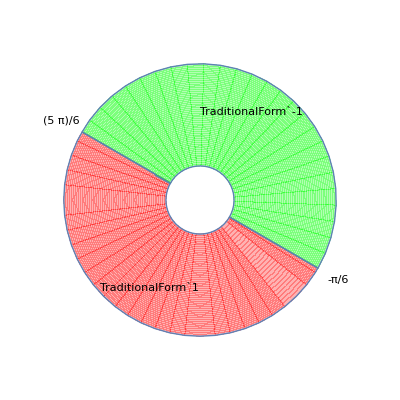
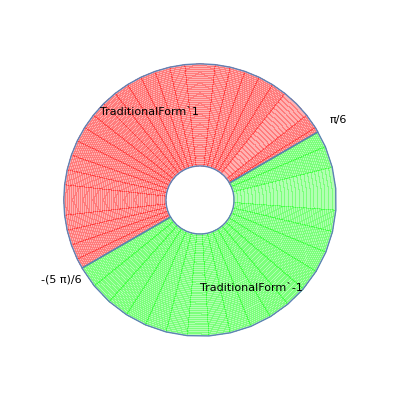
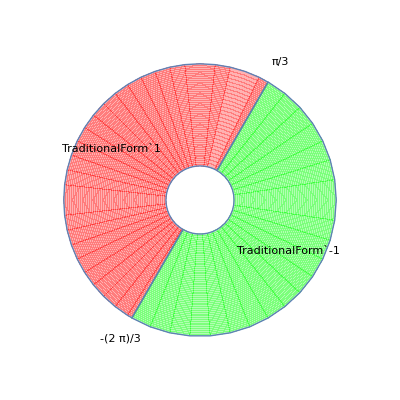
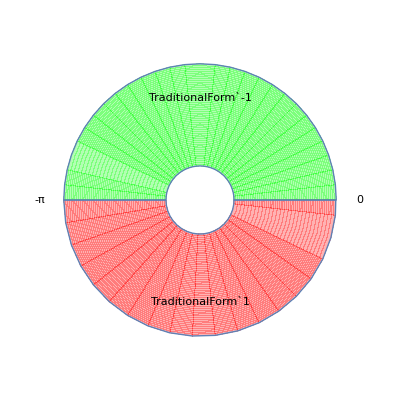
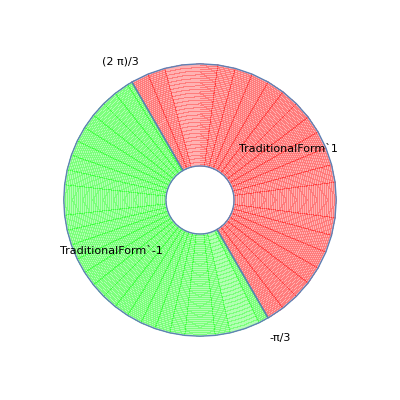
```mathematica
({{1, 1, 1}, {-Graphics-, -Graphics-, -Graphics-}, {-Graphics-, -Graphics-, -Graphics-}})
```

We have a source which makes discrete steps of 1/srcRange the question is to what degree of precision do we need to represent the transformation given that we require a precision of 1/wrkRange. What is required is the smallest number which can result from the transformation of a unit cube!

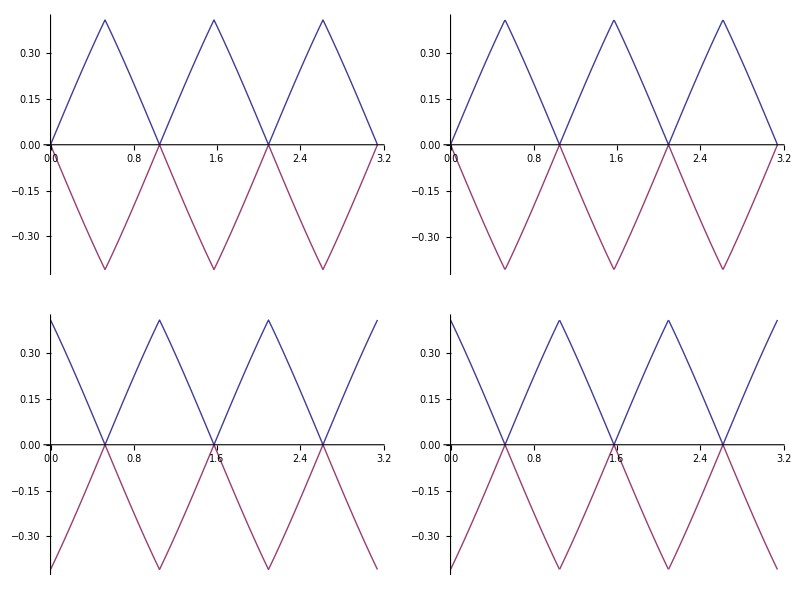

```mathematica
Grid[{{Plot[{Min[Abs[RGBCube[YAB][θ ][[3,{2,3,4,5,6,7}]]]],-Min[Abs[RGBCube[YAB][θ ][[3,{2,3,4,5,6,7}]]]]},{θ,0,Pi}], Plot[{√(2/3)Abs[Sin[Mod[θ+ Pi/6,Pi/3]- Pi/6]],-√(2/3)Abs[Sin[Mod[θ+ Pi/6,Pi/3]- Pi/6]]},{θ,0,Pi}]},{Plot[{Min[Abs[RGBCube[YAB][θ ][[2,{2,3,4,5,6,7}]]]],-Min[Abs[RGBCube[YAB][θ ][[2,{2,3,4,5,6,7}]]]]},{θ,0,Pi}],Plot[{√(2/3)Abs[Sin[Mod[θ,Pi/3]- Pi/6]],-√(2/3)Abs[Sin[Mod[θ,Pi/3]- Pi/6]]},{θ,0,Pi}]}}]
```

The error in the representation of the rotation matrix is

```mathematica
Clear[d];d[val_,n_]:=Round[(val * n)]/n;
Manipulate[StringJoin[  ToString[srcRange]," ( ",mForm[ N[d[YAB[θ],srcRange]]]," - ",mForm[N[YAB[θ]]],") = ",mForm[srcRange(N[d[YAB[θ],srcRange]]- N[YAB[θ]])]],{θ,0,Pi},{{srcRange,64},1,255,1}]
```

Channels 2 and 3 sum to zero meaning that the elements always contain opposite signs.

```mathematica
maskPos=Function[{θ},Evaluate[Map[Reduce[{#1>0,0 ≤θ <2Pi},θ]&,YAB[θ],{2}]]];
maskNeg=Function[{θ},Evaluate[Map[Reduce[{#1<0,0 ≤θ <2Pi},θ]&,YAB[θ],{2}]]];
MatrixForm[maskPos[θ]]
MatrixForm[maskNeg[θ]]
```

(0≤θ<2 π | 0≤θ<2 π | 0≤θ<2 π
(5 π)/6<θ<(11 π)/6 | 0≤θ<π/2||(3 π)/2<θ<2 π | π/6<θ<(7 π)/6
π/3<θ<(4 π)/3 | π<θ<2 π | 0≤θ<(2 π)/3||(5 π)/3<θ<2 π)

(False | False | False
0≤θ<(5 π)/6||(11 π)/6<θ<2 π | π/2<θ<(3 π)/2 | 0≤θ<π/6||(7 π)/6<θ<2 π
0≤θ<π/3||(4 π)/3<θ<2 π | 0<θ<π | (2 π)/3<θ<(5 π)/3)

```mathematica
partShow[Piecewise[{{mForm[Sign[nonNegativeSign[rR[Pi/12]]]], Inequality[0, LessEqual, θ, Less, Pi/6]}, 
   {mForm[Sign[nonNegativeSign[rR[Pi/4]]]], Inequality[Pi/6, LessEqual, θ, Less, Pi/3]}, 
   {mForm[Sign[nonNegativeSign[rR[(5*Pi)/12]]]], Inequality[Pi/3, LessEqual, θ, Less, Pi/2]}, 
   {mForm[Sign[nonNegativeSign[rR[(7*Pi)/12]]]], Inequality[Pi/2, LessEqual, θ, Less, (2*Pi)/3]}, 
   {mForm[Sign[nonNegativeSign[rR[(3*Pi)/4]]]], Inequality[(2*Pi)/3, LessEqual, θ, Less, (5*Pi)/6]}, 
   {mForm[Sign[nonNegativeSign[rR[(11*Pi)/12]]]], Inequality[(5*Pi)/6, LessEqual, θ, Less, Pi]}, 
   {mForm[Sign[nonNegativeSign[rR[(13*Pi)/12]]]], Inequality[Pi, LessEqual, θ, Less, (7*Pi)/6]}, 
   {mForm[Sign[nonNegativeSign[rR[(5*Pi)/4]]]], Inequality[(7*Pi)/6, LessEqual, θ, Less, (4*Pi)/3]}, 
   {mForm[Sign[nonNegativeSign[rR[(17*Pi)/12]]]], Inequality[(4*Pi)/3, LessEqual, θ, Less, (3*Pi)/2]}, 
   {mForm[Sign[nonNegativeSign[rR[(19*Pi)/12]]]], Inequality[(3*Pi)/2, LessEqual, θ, Less, (5*Pi)/3]}, 
   {mForm[Sign[nonNegativeSign[rR[(7*Pi)/4]]]], Inequality[(5*Pi)/3, LessEqual, θ, Less, (11*Pi)/6]}, 
   {mForm[Sign[nonNegativeSign[rR[(23*Pi)/12]]]], Inequality[(11*Pi)/6, LessEqual, θ, Less, 2*Pi]}}, Null]]
```

-Graphics-

```mathematica
Clear[splitCircle]
splitCircle[i_, θ_, val_:1] := Module[{showA, evalA, showB, evalB}, 
   Piecewise[{{val, CircularInequality[i*(Pi/6), LessEqual, θ, Less, (i + 6)*(Pi/6)]}, 
     {-val, CircularInequality[(i - 6)*(Pi/6), LessEqual, θ, Less, i*(Pi/6)]}}, Null]]
```

```mathematica
posNegCond=Function[{θ},Evaluate[{{1,1,1},{splitCircle[5,θ],splitCircle[9,θ],splitCircle[1,θ]},
{splitCircle[2,θ],splitCircle[6,θ,1],splitCircle[10,θ,1]}}]];
TraditionalForm[MatrixForm[posNegCond[θ]]]
```

(1 | 1 | 1
Piecewise[{{1, (5 π)/6≤θ<(11 π)/6}, {-1, -π/6≤θ<(5 π)/6}, {Null, True}}] | Piecewise[{{1, -π/2≤θ<π/2}, {-1, π/2≤θ<(3 π)/2}, {Null, True}}] | Piecewise[{{1, π/6≤θ<(7 π)/6}, {-1, -(5 π)/6≤θ<π/6}, {Null, True}}]
Piecewise[{{1, π/3≤θ<(4 π)/3}, {-1, -(2 π)/3≤θ<π/3}, {Null, True}}] | Piecewise[{{1, -π≤θ<0}, {-1, 0≤θ<π}, {Null, True}}] | Piecewise[{{1, -π/3≤θ<(2 π)/3}, {-1, (2 π)/3≤θ<(5 π)/3}, {Null, True}}])

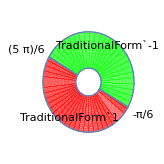
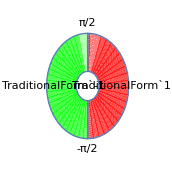
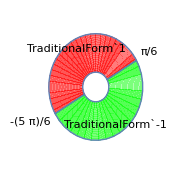
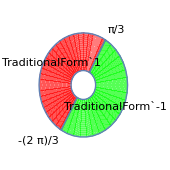
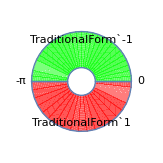
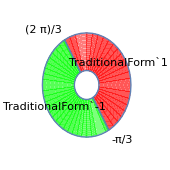
(1 | 1 | 1
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-)

```mathematica
MatrixForm[{{1,1,1},{partShow[splitCircle[5,θ]],partShow[splitCircle[9,θ]],partShow[splitCircle[1,θ]]},
{partShow[splitCircle[2,θ]],partShow[splitCircle[6,θ,1]],partShow[splitCircle[10,θ,1]]}}]
```

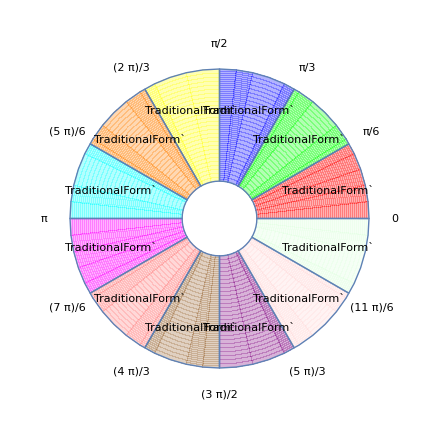

```mathematica
partShow[Piecewise[Table[{mForm[posNegCond[i Pi/6+Pi/12]], Inequality[i Pi/6, LessEqual, θ, Less, (i+1) Pi/6]},{i,0,11}], Null]]
```

To trace the origin of the error we need to know which elements in a row share the same sign.

```mathematica
Manipulate[{StringJoin["R[",ToString[θ,TraditionalForm],"] = ",mForm[colorMat[rR[θ]]]],StringJoin[ToString[1/2,TraditionalForm],"(",mForm[Sign[nonNegativeSign[rR[θ]].{1,1,1}]],"⊗",mForm[nonNegativeSign[rR[θ]]],"+1) = "," = ",mForm[matSameSign[rR[θ]]]]},{θ,0,2 Pi,Pi/12}]
```

```mathematica
partShow[Piecewise[{
{mForm[matSameSign[rR[Pi/12]]], Inequality[0, LessEqual, θ, Less, Pi/6]||Inequality[         Pi       , LessEqual, θ, Less, (7*Pi)/6]}, 
   {mForm[matSameSign[rR[        Pi   /  4  ]]], Inequality[        Pi/  6, LessEqual, θ, Less, Pi/3]||Inequality[(7*Pi)/6, LessEqual, θ, Less, (4*Pi)/3]}, 
   {mForm[matSameSign[rR[(  5*Pi)/12]]], Inequality[        Pi/  3, LessEqual, θ, Less, Pi/2]||Inequality[(4*Pi)/3, LessEqual, θ, Less, (3*Pi)/2]}, 
   {mForm[matSameSign[rR[(  7*Pi)/12]]], Inequality[        Pi/  2, LessEqual, θ, Less, (2*Pi)/3]||Inequality[(3*Pi)/2, LessEqual, θ, Less, (5*Pi)/3]}, 
   {mForm[matSameSign[rR[(  3*Pi)/  4]]], Inequality[(2*Pi)/3, LessEqual, θ, Less, (5*Pi)/6]||Inequality[(5*Pi)/3, LessEqual, θ, Less, (11*Pi)/6]}, 
   {mForm[matSameSign[rR[(11*Pi)/12]]], Inequality[(5*Pi)/6, LessEqual, θ, Less, Pi]||Inequality[(11*Pi)/6, LessEqual, θ, Less, 2*Pi]}}, Null]]
```

-Graphics-

```mathematica
sameLoc[θ_]:=Piecewise[{{{Null,2,3}, Inequality[0, LessEqual, θ, Less, Pi/6] || Inequality[Pi, LessEqual, θ, Less, (7*Pi)/6]}, 
   {{Null,1,3}, Inequality[Pi/6, LessEqual, θ, Less, Pi/3] || Inequality[(7*Pi)/6, LessEqual, θ, Less, (4*Pi)/3]}, 
   {{Null,1,2}, Inequality[Pi/3, LessEqual, θ, Less, Pi/2] || Inequality[(4*Pi)/3, LessEqual, θ, Less, (3*Pi)/2]}, 
   {{Null,3,2}, Inequality[Pi/2, LessEqual, θ, Less, (2*Pi)/3] || Inequality[(3*Pi)/2, LessEqual, θ, Less, (5*Pi)/3]}, 
   {{Null,3,1}, Inequality[(2*Pi)/3, LessEqual, θ, Less, (5*Pi)/6] || Inequality[(5*Pi)/3, LessEqual, θ, Less, (11*Pi)/6]}, 
   {{Null,2,1}, Inequality[(5*Pi)/6, LessEqual, θ, Less, Pi] || Inequality[(11*Pi)/6, LessEqual, θ, Less, 2*Pi]}}, Null]
```

Clear::ssym: scale["rR", "fR"] is not a symbol or a string.

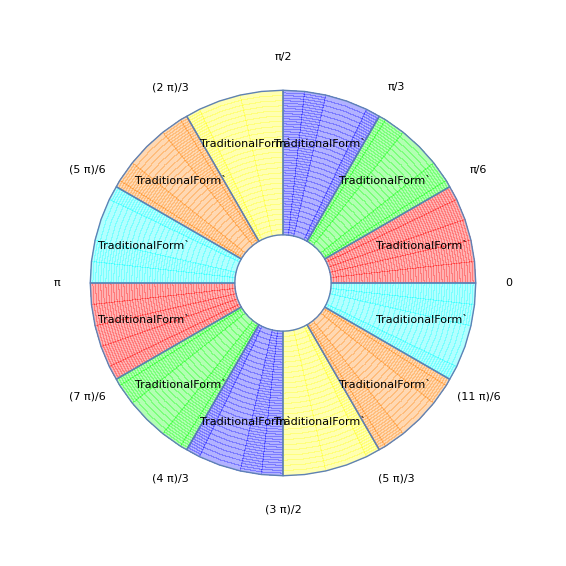

```mathematica
Clear[scale["rR","fR"],θ];
scale["rR","fR"]=Function[θ,Evaluate[Piecewise@Table[{{1,rR[θ]⟦2,sameLoc[i]⟦2⟧⟧,rR[θ]⟦3,sameLoc[i]⟦3⟧⟧},i-π/12≤Mod[θ,2 Pi]<i+π/12||i+(11 π)/12≤Mod[θ,2 Pi]<i+(13 π)/12},{i,π/12,(11 π)/12,π/6}]]];
partShow[ApplyToPiecewise[mForm,scale["rR","fR"][θ]]]
```

```mathematica
fR=Function[{θ},Evaluate[ApplyToPiecewise[(rR[θ]/#)&,scale["rR","fR"][θ]]]];
```

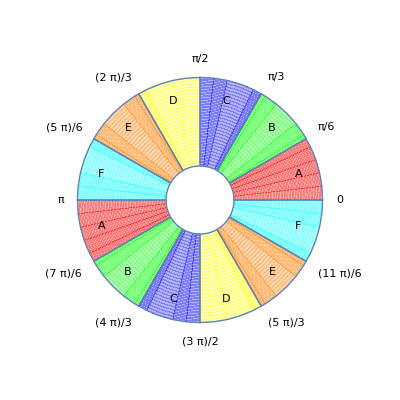
The Factored Rotation in each π/6 Region
-Graphics- | Scale : fS[θ] | Factored Rotation : fR[θ]
A | 1
cos(θ)
cos(π/6 - θ) | (1 | 1 | 1
-sec(θ) sin(θ+π/6) | 1 | -sec(θ) sin(π/6-θ)
-cos(θ+π/6) sec(π/6-θ) | -sec(π/6-θ) sin(θ) | 1)
B | 1
-sin(θ + π/6)
cos(π/6 - θ) | (1 | 1 | 1
1 | -cos(θ) csc(θ+π/6) | csc(θ+π/6) sin(π/6-θ)
-cos(θ+π/6) sec(π/6-θ) | -sec(π/6-θ) sin(θ) | 1)
C | 1
-sin(θ + π/6)
-sin(θ) | (1 | 1 | 1
1 | -cos(θ) csc(θ+π/6) | csc(θ+π/6) sin(π/6-θ)
cos(θ+π/6) csc(θ) | 1 | -cos(π/6-θ) csc(θ))
D | 1
-sin(π/6 - θ)
-sin(θ) | (1 | 1 | 1
csc(π/6-θ) sin(θ+π/6) | -cos(θ) csc(π/6-θ) | 1
cos(θ+π/6) csc(θ) | 1 | -cos(π/6-θ) csc(θ))
E | 1
-sin(π/6 - θ)
-cos(θ + π/6) | (1 | 1 | 1
csc(π/6-θ) sin(θ+π/6) | -cos(θ) csc(π/6-θ) | 1
1 | sec(θ+π/6) sin(θ) | -cos(π/6-θ) sec(θ+π/6))
F | 1
cos(θ)
-cos(θ + π/6) | (1 | 1 | 1
-sec(θ) sin(θ+π/6) | 1 | -sec(θ) sin(π/6-θ)
1 | sec(θ+π/6) sin(θ) | -cos(π/6-θ) sec(θ+π/6))

```mathematica
lbls=Map[Style[#,FontSize->Large]&,{"A","B","C","D","E","F"}];
Row[{Column[{Text[Style["The Factored Rotation in each π/6 Region",FontSize->Large]],
partShow[Piecewise[{{lbls[[1]],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{lbls[[2]],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{lbls[[3]],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{lbls[[4]],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{lbls[[5]],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{lbls[[6]],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]]}],
TableForm[{
{mForm[scale["rR","fR"][θ][[1,1,1]]],TraditionalForm[fR[θ][[1,1,1]]]},
{mForm[scale["rR","fR"][θ][[1,2,1]]],TraditionalForm[fR[θ][[1,2,1]]]},
{mForm[scale["rR","fR"][θ][[1,3,1]]],TraditionalForm[fR[θ][[1,3,1]]]},
{mForm[scale["rR","fR"][θ][[1,4,1]]],TraditionalForm[fR[θ][[1,4,1]]]},
{mForm[scale["rR","fR"][θ][[1,5,1]]],TraditionalForm[fR[θ][[1,5,1]]]},
{mForm[scale["rR","fR"][θ][[1,6,1]]],TraditionalForm[fR[θ][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fS[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ]",FontWeight->Bold]}]}},TableAlignments->Center]}]
```

```mathematica
ApplyToPiecewise[mForm,fR[θ]]
```

Piecewise[{{1 | 1 | 1
sin(θ + π/6) (-sec(θ)) | 1 | sin(π/6 - θ) (-sec(θ))
-cos(θ + π/6) sec(π/6 - θ) | sin(θ) (-sec(π/6 - θ)) | 1, 0≤Mod[θ,2 π]<π/6||π≤Mod[θ,2 π]<(7 π)/6}, {1 | 1 | 1
1 | -cos(θ) csc(θ + π/6) | sin(π/6 - θ) csc(θ + π/6)
-cos(θ + π/6) sec(π/6 - θ) | sin(θ) (-sec(π/6 - θ)) | 1, π/6≤Mod[θ,2 π]<π/3||(7 π)/6≤Mod[θ,2 π]<(4 π)/3}, {1 | 1 | 1
1 | -cos(θ) csc(θ + π/6) | sin(π/6 - θ) csc(θ + π/6)
cos(θ + π/6) csc(θ) | 1 | -cos(π/6 - θ) csc(θ), π/3≤Mod[θ,2 π]<π/2||(4 π)/3≤Mod[θ,2 π]<(3 π)/2}, {1 | 1 | 1
sin(θ + π/6) csc(π/6 - θ) | -cos(θ) csc(π/6 - θ) | 1
cos(θ + π/6) csc(θ) | 1 | -cos(π/6 - θ) csc(θ), π/2≤Mod[θ,2 π]<(2 π)/3||(3 π)/2≤Mod[θ,2 π]<(5 π)/3}, {1 | 1 | 1
sin(θ + π/6) csc(π/6 - θ) | -cos(θ) csc(π/6 - θ) | 1
1 | sin(θ) sec(θ + π/6) | -cos(π/6 - θ) sec(θ + π/6), (2 π)/3≤Mod[θ,2 π]<(5 π)/6||(5 π)/3≤Mod[θ,2 π]<(11 π)/6}, {1 | 1 | 1
sin(θ + π/6) (-sec(θ)) | 1 | sin(π/6 - θ) (-sec(θ))
1 | sin(θ) sec(θ + π/6) | -cos(π/6 - θ) sec(θ + π/6), (5 π)/6≤Mod[θ,2 π]<π||(11 π)/6≤Mod[θ,2 π]<2 π}, {0, True}}]

Let δθ = Mod[θ,Pi/6]
Let Θ = θ-δθ
then
θ = Θ+δθ
also the regions can be simplified by noticing that they are in modulo π arithmatic so θ→Mod[θ,π]

```mathematica
ffR=Function[{θ},Evaluate[
Piecewise@Table[{Assuming[Element[δθ,Reals]&& δθ≥ 0 && δθ< Pi/6,FullSimplify[fR[θ][[1,i+1,1]]/.{θ->i Pi/6 +δθ}]],FullSimplify[fR[θ][[1,i+1,2,1]]/.{Mod[θ,2 π]-> Mod[θ,π]} ]},{i,0,5}]]];
ApplyToPiecewise[mForm,ffR[θ]]
```

Piecewise[{{1 | 1 | 1
sin(δθ + π/6) (-sec(δθ)) | 1 | 1/2 (√3 tan(δθ) - 1)
-cos(δθ + π/6) sec(π/6 - δθ) | sin(δθ) (-sec(π/6 - δθ)) | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | -cos(δθ + π/6) sec(π/6 - δθ) | sin(δθ) (-sec(π/6 - δθ))
1/2 (√3 tan(δθ) - 1) | sin(δθ + π/6) (-sec(δθ)) | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | 1/2 (√3 tan(δθ) - 1) | sin(δθ + π/6) (-sec(δθ))
sin(δθ) (-sec(π/6 - δθ)) | 1 | -cos(δθ + π/6) sec(π/6 - δθ), π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
-cos(δθ + π/6) sec(π/6 - δθ) | sin(δθ) (-sec(π/6 - δθ)) | 1
sin(δθ + π/6) (-sec(δθ)) | 1 | 1/2 (√3 tan(δθ) - 1), π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
1/2 (√3 tan(δθ) - 1) | sin(δθ + π/6) (-sec(δθ)) | 1
1 | -cos(δθ + π/6) sec(π/6 - δθ) | sin(δθ) (-sec(π/6 - δθ)), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
sin(δθ) (-sec(π/6 - δθ)) | 1 | -cos(δθ + π/6) sec(π/6 - δθ)
1 | 1/2 (√3 tan(δθ) - 1) | sin(δθ + π/6) (-sec(δθ)), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

There are only 4 functions

```mathematica
Clear[ffRList,fReq,fRe,ffRe]
```

```mathematica
ffRList=Function[{δθ},Evaluate@ApplyToPiecewise[Union[Flatten[#]]&,ffR[θ]][[1,1,1]]]
```

Function[{δθ},{1,-Cos[π/6+δθ] Sec[π/6-δθ],-Sec[π/6-δθ] Sin[δθ],-Sec[δθ] Sin[π/6+δθ],1/2 (-1+√3 Tan[δθ])}]

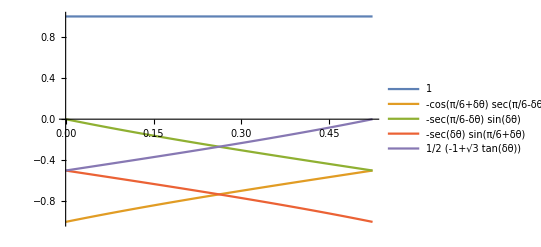

```mathematica
Plot[Evaluate[ffRList[δθ]],{δθ,0,Pi/6},PlotLegends->"Expressions"]
```

using

```mathematica
FullSimplify[-Cos[π/6+δθ] Sec[π/6-δθ]==-1/2 (1+√3 Tan[π/6-δθ])]
FullSimplify[-Sec[π/6-δθ] Sin[δθ] ==-1/2 (1+√3 Tan[δθ-π/6])]
FullSimplify[-Sec[δθ] Sin[π/6+δθ]==-1/2 (1+√3 Tan[δθ])]
```

True

True

True

Defining a common function for the elements

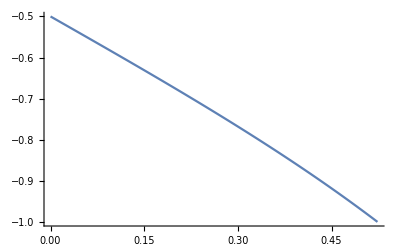

```mathematica
fRe=Function[{θ},-1/2 (1+√3 Tan[θ])];
Plot[Evaluate[fRe[θ]],{θ,0,Pi/6},PlotLegends->"Expressions"]
```

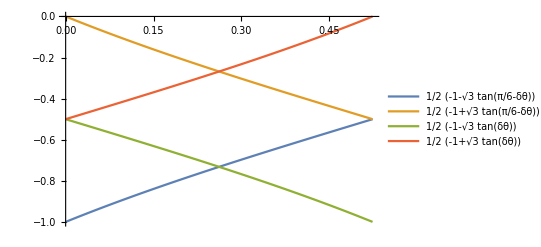

```mathematica
fReList=Function[{δθ},{fRe[π/6-δθ],fRe[δθ-π/6],fRe[δθ],fRe[-δθ]}];
Plot[Evaluate[fReList[δθ]],{δθ,0,Pi/6},PlotLegends->"Expressions"]
```

we can write fR as

```mathematica
ffRe=Function[{θ,δθ,fReqq},Evaluate[ApplyToPiecewise[
(#/.{-Cos[π/6+δθ] Sec[π/6-δθ]-> fReqq[π/6-δθ],-Sec[π/6-δθ] Sin[δθ]-> fReqq[δθ-π/6],-Sec[δθ] Sin[π/6+δθ]-> fReqq[δθ],1/2 (-1+√3 Tan[δθ])-> fReqq[-δθ]})&,ffR[θ]]]];
```

```mathematica
mForm[ffRe[θ,Mod[θ,Pi/6],fRe]]
```

…

```mathematica
Row[{"fR(θ) = ",mForm[ffRe[θ,δθ,"fRe"]]}]
```

fR(θ) = Piecewise[{{1 | 1 | 1
fRe | 1 | fRe
fRe | fRe | 1, 0}, {1 | 1 | 1
1 | fRe | fRe
fRe | fRe | 1, π}, {1 | 1 | 1
1 | fRe | fRe
fRe | 1 | fRe, π}, {1 | 1 | 1
fRe | fRe | 1
fRe | 1 | fRe, π}, {1 | 1 | 1
fRe | fRe | 1
1 | fRe | fRe, 2 π/3 ≤ TemplateBox[List[}, {1 | 1 | 1
fRe | 1 | fRe
1 | fRe | fRe, 5 π/6 ≤ TemplateBox[List[}}]

The Relationship

```mathematica
Reduce[-1-fRe[θ]==fRe[-θ]]
```

True

```mathematica
mForm[ffRe[θ,δθ,"fRe"]]
```

Piecewise[{{1 | 1 | 1
fRe | 1 | -
fRe | - | 1, 0}, {1 | 1 | 1
1 | fRe | -
- | fRe | 1, π}, {1 | 1 | 1
1 | - | fRe
- | 1 | fRe, π}, {1 | 1 | 1
fRe | - | 1
fRe | 1 | -, π}, {1 | 1 | 1
- | fRe | 1
1 | fRe | -, 2 π/3 ≤ TemplateBox[List[}, {1 | 1 | 1
- | 1 | fRe
1 | - | fRe, 5 π/6 ≤ TemplateBox[List[}}]

```mathematica
ffRe=Function[{θ,δθ,fReqq},Evaluate[ApplyToPiecewise[
(#/.{ fReqq[δθ-π/6]-> -1-fReqq[π/6-δθ], fReqq[-δθ]-> -1-fReqq[δθ]})&,ffRe[θ,δθ,fReqq]]]];
```

```mathematica
Clear[m];fRO=Function[{m,θ},Evaluate[ffRe[θ,δθ,f]/.{f[δθ]-> m[[2,1]],f[-δθ]->m[[2,3]],f[π/6-δθ]-> m[[3,1]],f[-π/6+δθ]-> m[[3,2]],{1,1,1}->{m[[1,1]],m[[1,2]],m[[1,3]]}}]];
fRa=Function[{δθ,f},Evaluate[ffRe[θ,δθ,f][[1,1,1]]]];
scale["rR","ffR"]=Function[{θ},Evaluate[
Piecewise@Table[{Assuming[Element[δθ,Reals]&& δθ≥ 0 && δθ< Pi/6,FullSimplify[scale["rR","fR"][θ][[1,i+1,1]]/.{θ->i Pi/6 +δθ}]],FullSimplify[scale["rR","fR"][θ][[1,i+1,2,1]]/.{Mod[θ,2 π]-> Mod[θ,π]} ]},{i,0,5}]]];
fSe= Function[{δθ},{1,Cos[δθ],Cos[π/6-δθ]}];
fSO = Function[{m, θ}, Evaluate[
scale["rR","ffR"][θ]/.{Cos[δθ]-> m[[2]],Cos[π/6-δθ]-> m[[3]]}]];
mForm[fSO[fSe[δθ],θ]]
mForm[fRO[fRa[δθ,"fRe"],θ]]
```

Piecewise[{{{1, cos(δθ), cos(π/6 - δθ)}, 0}, {{1, -cos(π/6 - δθ), cos(δθ)}, π}, {{1, -cos(δθ), -cos(π/6 - δθ)}, π}, {{1, cos(π/6 - δθ), -cos(δθ)}, π}, {{1, cos(δθ), cos(π/6 - δθ)}, 2 π/3 ≤ TemplateBox[List[}, {{1, -cos(π/6 - δθ), cos(δθ)}, 5 π/6 ≤ TemplateBox[List[}}]

Piecewise[{{1 | 1 | 1
fRe | 1 | fRe
fRe | fRe | 1, 0}, {1 | 1 | 1
1 | fRe | fRe
fRe | fRe | 1, π}, {1 | 1 | 1
1 | fRe | fRe
fRe | 1 | fRe, π}, {1 | 1 | 1
fRe | fRe | 1
fRe | 1 | fRe, π}, {1 | 1 | 1
fRe | fRe | 1
1 | fRe | fRe, 2 π/3 ≤ TemplateBox[List[}, {1 | 1 | 1
fRe | 1 | fRe
1 | fRe | fRe, 5 π/6 ≤ TemplateBox[List[}}]

```mathematica
ApplyToPiecewise[mForm[#]&,fSO[fSe[δθ],θ]]
```

Piecewise[{{1
cos(δθ)
cos(π/6 - δθ), 0≤Mod[θ,π]<π/6}, {1
-cos(π/6 - δθ)
cos(δθ), π/6≤Mod[θ,π]<π/3}, {1
-cos(δθ)
-cos(π/6 - δθ), π/3≤Mod[θ,π]<π/2}, {1
cos(π/6 - δθ)
-cos(δθ), π/2≤Mod[θ,π]<(2 π)/3}, {1
cos(δθ)
cos(π/6 - δθ), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-cos(π/6 - δθ)
cos(δθ), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

So we have

```mathematica
Definition[fRe]
Definition[fRa]
Definition[fRO]
```

fRe=Function[{θ},-1/2 (1+√3 Tan[θ])]

fRa=Function[{δθ,f},{{1,1,1},{f[δθ],1,f[-δθ]},{f[π/6-δθ],f[-π/6+δθ],1}}]

fRO=Function[{m,θ},Piecewise[{{{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦2,1⟧,1,m⟦2,3⟧},{m⟦3,1⟧,m⟦3,2⟧,1}}, 0≤Mod[θ,π]<π/6}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{1,m⟦3,1⟧,m⟦3,2⟧},{m⟦2,3⟧,m⟦2,1⟧,1}}, π/6≤Mod[θ,π]<π/3}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{1,m⟦2,3⟧,m⟦2,1⟧},{m⟦3,2⟧,1,m⟦3,1⟧}}, π/3≤Mod[θ,π]<π/2}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦3,1⟧,m⟦3,2⟧,1},{m⟦2,1⟧,1,m⟦2,3⟧}}, π/2≤Mod[θ,π]<(2 π)/3}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦2,3⟧,m⟦2,1⟧,1},{1,m⟦3,1⟧,m⟦3,2⟧}}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦3,2⟧,1,m⟦3,1⟧},{1,m⟦2,3⟧,m⟦2,1⟧}}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]]

```mathematica
fRO=Function[{m,θ},Piecewise[{{{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦2,1⟧,m[[2,2]],m⟦2,3⟧},{m⟦3,1⟧,m⟦3,2⟧,m[[3,3]]}}, 0≤Mod[θ,π]<π/6}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m[[3,3]],m⟦3,1⟧,m⟦3,2⟧},{m⟦2,3⟧,m⟦2,1⟧,m[[2,2]]}}, π/6≤Mod[θ,π]<π/3}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m[[2,2]],m⟦2,3⟧,m⟦2,1⟧},{m⟦3,2⟧,m[[3,3]],m⟦3,1⟧}}, π/3≤Mod[θ,π]<π/2}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦3,1⟧,m⟦3,2⟧,m[[3,3]]},{m⟦2,1⟧,m[[2,2]],m⟦2,3⟧}}, π/2≤Mod[θ,π]<(2 π)/3}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦2,3⟧,m⟦2,1⟧,m[[2,2]]},{m[[3,3]],m⟦3,1⟧,m⟦3,2⟧}}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧},{m⟦3,2⟧,m[[3,3]],m⟦3,1⟧},{m[[2,2]],m⟦2,3⟧,m⟦2,1⟧}}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]];
```

```mathematica
fSe= Function[{δθ},{1,Cos[δθ],Cos[π/6-δθ]}];
fSO = Function[{m, θ}, Piecewise[{{{1, m[[2]], m[[3]]}, Inequality[0, LessEqual, 
       Mod[θ, Pi], Less, Pi/6]}, {{1, -m[[3]], m[[2]]}, Inequality[Pi/6, LessEqual, 
       Mod[θ, Pi], Less, Pi/3]}, {{1, -m[[2]], -m[[3]]}, Inequality[Pi/3, LessEqual, 
       Mod[θ, Pi], Less, Pi/2]}, {{1, m[[3]], -m[[2]]}, Inequality[Pi/2, LessEqual, 
       Mod[θ, Pi], Less, (2*Pi)/3]}, {{1, m[[2]], m[[3]]}, 
      Inequality[(2*Pi)/3, LessEqual, Mod[θ, Pi], Less, (5*Pi)/6]}, 
     {{1, -m[[3]], m[[2]]}, Inequality[(5*Pi)/6, LessEqual, Mod[θ, Pi], Less, Pi]}}, 0]];
fSO[fSe[δθ],θ]
```

```mathematica
m={{1,1,1},{a,1,α},{b,β,1}};
δm={{0,0,0},{a,0,-a},{b,-b,0}};
TraditionalForm@Column[{
Row[{"fR(θ) = fRO( fRa( δθ, fRe))"}],
Row[{"δθ = ",Mod[θ,π/6]}],
Row[{"fRe(ϕ) = ",fRe[ϕ]}],
Row[{"fRa"[ϕ, f]," = ",fRa[ϕ,f]}],
Row[{"fRO"[mForm[m],θ]," = ",fRO[m,θ]}],
Row[{"fRO"[mForm[δm],θ]," = ",fRO[δm,θ]}]
}]
```

fR(θ) = fRO( fRa( δθ, fRe))
δθ = θπ/6
fRe(ϕ) = 1/2 (-√3 tan(ϕ)-1)
fRa(ϕ,f) = (1 | 1 | 1
f(ϕ) | 1 | f(-ϕ)
f(π/6-ϕ) | f(ϕ-π/6) | 1)
fRO(1 | 1 | 1
a | 1 | α
b | β | 1,θ) = Piecewise[{{(1 | 1 | 1
a | 1 | α
b | β | 1), 0≤θπ<π/6}, {(1 | 1 | 1
1 | b | β
α | a | 1), π/6≤θπ<π/3}, {(1 | 1 | 1
1 | α | a
β | 1 | b), π/3≤θπ<π/2}, {(1 | 1 | 1
b | β | 1
a | 1 | α), π/2≤θπ<(2 π)/3}, {(1 | 1 | 1
α | a | 1
1 | b | β), (2 π)/3≤θπ<(5 π)/6}, {(1 | 1 | 1
β | 1 | b
1 | α | a), (5 π)/6≤θπ<π}}]
fRO(0 | 0 | 0
a | 0 | -a
b | -b | 0,θ) = Piecewise[{{(0 | 0 | 0
a | 0 | -a
b | -b | 0), 0≤θπ<π/6}, {(0 | 0 | 0
0 | b | -b
-a | a | 0), π/6≤θπ<π/3}, {(0 | 0 | 0
0 | -a | a
-b | 0 | b), π/3≤θπ<π/2}, {(0 | 0 | 0
b | -b | 0
a | 0 | -a), π/2≤θπ<(2 π)/3}, {(0 | 0 | 0
-a | a | 0
0 | b | -b), (2 π)/3≤θπ<(5 π)/6}, {(0 | 0 | 0
-b | 0 | b
0 | -a | a), (5 π)/6≤θπ<π}}]

```mathematica
TraditionalForm[Row[{"fRO"[δm,θ]," = ",fRO[δm,θ]}]]
TeXForm[fRO[δm,θ]]
```

fRO((0 | 0 | 0
a | 0 | -a
b | -b | 0),θ) = Piecewise[{{(0 | 0 | 0
a | 0 | -a
b | -b | 0), 0≤θπ<π/6}, {(0 | 0 | 0
0 | b | -b
-a | a | 0), π/6≤θπ<π/3}, {(0 | 0 | 0
0 | -a | a
-b | 0 | b), π/3≤θπ<π/2}, {(0 | 0 | 0
b | -b | 0
a | 0 | -a), π/2≤θπ<(2 π)/3}, {(0 | 0 | 0
-a | a | 0
0 | b | -b), (2 π)/3≤θπ<(5 π)/6}, {(0 | 0 | 0
-b | 0 | b
0 | -a | a), (5 π)/6≤θπ<π}}]

```mathematica
M=({{0, 0, 0}, {dd, ee, ff}, {gg, hh, ii}});
Table[sol[i]=(M/.Solve[Reduce[M.fRO[δm,θ][[1,i,1]]==fRO[δm,θ][[1,i+1,1]]&&a ≠ 0&&b≠0],{dd,gg,ee,ff,hh,ii}])[[1]],{i,1,5}]
```

{{{0,0,0},{dd,b/a,-1},{gg,0,-a/b}},{{0,0,0},{dd,-a/b,0},{gg,-1,b/a}},{{0,0,0},{dd,b/a,-1},{gg,0,-a/b}},{{0,0,0},{dd,-a/b,0},{gg,-1,b/a}},{{0,0,0},{dd,b/a,-1},{gg,0,-a/b}}}

```mathematica
Table[mForm[sol[i]],{i,1,5}]
```

{0 | 0 | 0
dd | b/a | -1
gg | 0 | -a/b,0 | 0 | 0
dd | -a/b | 0
gg | -1 | b/a,0 | 0 | 0
dd | b/a | -1
gg | 0 | -a/b,0 | 0 | 0
dd | -a/b | 0
gg | -1 | b/a,0 | 0 | 0
dd | b/a | -1
gg | 0 | -a/b}

```mathematica
MM=M/.{hh-> 0,ff-> -1,ee->b/a,ii-> -a/b};
MatrixForm[MM]
Reduce[MM.fRO[δm,θ][[1,2,1]]==fRO[δm,θ][[1,3,1]]&&a ≠ 0&&b≠0]
```

(0 | 0 | 0
dd | b/a | -1
gg | 0 | -a/b)

False

```mathematica
Inverse[fRO[δm,θ][[1,1,1]]]
```

Inverse[{{0,0,0},{a,0,-a},{b,-b,0}}]

```mathematica
Inverse[{{0,0,0},{a,0,-a},{b,-b,0}}]
```

Inverse[{{0,0,0},{a,0,-a},{b,-b,0}}]

The values at multiples of Pi/6 are ok

```mathematica
Table[{rR[i],Mod[θ,2 Pi]==i},{i,0,2 Pi,π/6}]
```

{{{{1,1,1},{-1/2,1,-1/2},{-(√3)/2,0,(√3)/2}},Mod[θ,2 π]==0},{{{1,1,1},{-(√3)/2,(√3)/2,0},{-1/2,-1/2,1}},Mod[θ,2 π]==π/6},{{{1,1,1},{-1,1/2,1/2},{0,-(√3)/2,(√3)/2}},Mod[θ,2 π]==π/3},{{{1,1,1},{-(√3)/2,0,(√3)/2},{1/2,-1,1/2}},Mod[θ,2 π]==π/2},{{{1,1,1},{-1/2,-1/2,1},{(√3)/2,-(√3)/2,0}},Mod[θ,2 π]==(2 π)/3},{{{1,1,1},{0,-(√3)/2,(√3)/2},{1,-1/2,-1/2}},Mod[θ,2 π]==(5 π)/6},{{{1,1,1},{1/2,-1,1/2},{(√3)/2,0,-(√3)/2}},Mod[θ,2 π]==π},{{{1,1,1},{(√3)/2,-(√3)/2,0},{1/2,1/2,-1}},Mod[θ,2 π]==(7 π)/6},{{{1,1,1},{1,-1/2,-1/2},{0,(√3)/2,-(√3)/2}},Mod[θ,2 π]==(4 π)/3},{{{1,1,1},{(√3)/2,0,-(√3)/2},{-1/2,1,-1/2}},Mod[θ,2 π]==(3 π)/2},{{{1,1,1},{1/2,1/2,-1},{-(√3)/2,(√3)/2,0}},Mod[θ,2 π]==(5 π)/3},{{{1,1,1},{0,(√3)/2,-(√3)/2},{-1,1/2,1/2}},Mod[θ,2 π]==(11 π)/6},{{{1,1,1},{-1/2,1,-1/2},{-(√3)/2,0,(√3)/2}},Mod[θ,2 π]==2 π}}

```mathematica
Table[{scale["rR","fR"][i],fR[i]},{i,0,2 Pi,π/6}]
```

{{{1,1,(√3)/2},{{1,1,1},{-1/2,1,-1/2},{-1,0,1}}},{{1,-(√3)/2,1},{{1,1,1},{1,-1,0},{-1/2,-1/2,1}}},{{1,-1,-(√3)/2},{{1,1,1},{1,-1/2,-1/2},{0,1,-1}}},{{1,(√3)/2,-1},{{1,1,1},{-1,0,1},{-1/2,1,-1/2}}},{{1,1,(√3)/2},{{1,1,1},{-1/2,-1/2,1},{1,-1,0}}},{{1,-(√3)/2,1},{{1,1,1},{0,1,-1},{1,-1/2,-1/2}}},{{1,-1,-(√3)/2},{{1,1,1},{-1/2,1,-1/2},{-1,0,1}}},{{1,(√3)/2,-1},{{1,1,1},{1,-1,0},{-1/2,-1/2,1}}},{{1,1,(√3)/2},{{1,1,1},{1,-1/2,-1/2},{0,1,-1}}},{{1,-(√3)/2,1},{{1,1,1},{-1,0,1},{-1/2,1,-1/2}}},{{1,-1,-(√3)/2},{{1,1,1},{-1/2,-1/2,1},{1,-1,0}}},{{1,(√3)/2,-1},{{1,1,1},{0,1,-1},{1,-1/2,-1/2}}},{{1,1,(√3)/2},{{1,1,1},{-1/2,1,-1/2},{-1,0,1}}}}

```mathematica
Manipulate[Column[{StringJoin["rR[",ToString[θ,TraditionalForm],"] = ",mForm[colorMat[rR[θ]]]],StringJoin[mForm[scale["rR","fR"][θ]],"⊗",mForm[fR[θ]]," == ",mForm[rR[θ]],If[rR[θ]== scale["rR","fR"][θ]  fR[θ],"✓","×"]]}],{θ,0,2 Pi}]
```

#### The quantized representation

fR has elements which are in the range -1 ... 1.
These can be scaled to an integer range for discrete representation as qR. 
The scale we choose depends on the bit depth of the target type. To sum three numbers of one type requires one bit per sum. If the src type is n bits and we wish to represent the matrix in the same type, allowing that the working type be 2n bits and not more, then the matrix must be represented in n-2 bits.

```mathematica
mForm[scale["qR","fR"][θ,n]]
```

1
2^n - 2
2^n - 2

```mathematica
qR=Function[{θ,δθ,f,n},Evaluate[ApplyToPiecewise[(Round[scale["qR","fR"][θ,n] #])&,ffRe[θ,δθ,f]]]];
```

```mathematica
Definition[qR]
```

qR=Function[{θ,δθ,f,n},Piecewise[{{{{1,1,1},{Round[2^(-2+n) f[δθ]],Round[2^(-2+n)],Round[2^(-2+n) f[-δθ]]},{Round[2^(-2+n) f[π/6-δθ]],Round[2^(-2+n) f[-π/6+δθ]],Round[2^(-2+n)]}}, 0≤Mod[θ,π]<π/6}, {{{1,1,1},{Round[2^(-2+n)],Round[2^(-2+n) f[π/6-δθ]],Round[2^(-2+n) f[-π/6+δθ]]},{Round[2^(-2+n) f[-δθ]],Round[2^(-2+n) f[δθ]],Round[2^(-2+n)]}}, π/6≤Mod[θ,π]<π/3}, {{{1,1,1},{Round[2^(-2+n)],Round[2^(-2+n) f[-δθ]],Round[2^(-2+n) f[δθ]]},{Round[2^(-2+n) f[-π/6+δθ]],Round[2^(-2+n)],Round[2^(-2+n) f[π/6-δθ]]}}, π/3≤Mod[θ,π]<π/2}, {{{1,1,1},{Round[2^(-2+n) f[π/6-δθ]],Round[2^(-2+n) f[-π/6+δθ]],Round[2^(-2+n)]},{Round[2^(-2+n) f[δθ]],Round[2^(-2+n)],Round[2^(-2+n) f[-δθ]]}}, π/2≤Mod[θ,π]<(2 π)/3}, {{{1,1,1},{Round[2^(-2+n) f[-δθ]],Round[2^(-2+n) f[δθ]],Round[2^(-2+n)]},{Round[2^(-2+n)],Round[2^(-2+n) f[π/6-δθ]],Round[2^(-2+n) f[-π/6+δθ]]}}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{{1,1,1},{Round[2^(-2+n) f[-π/6+δθ]],Round[2^(-2+n)],Round[2^(-2+n) f[π/6-δθ]]},{Round[2^(-2+n)],Round[2^(-2+n) f[-δθ]],Round[2^(-2+n) f[δθ]]}}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]]

```mathematica
ApplyToPiecewise[mForm,qR[θ,δθ,f,n]]
```

Piecewise[{{1 | 1 | 1
Round[2^n - 2 f(δθ)] | 2^n - 2 | Round[2^n - 2 f(-δθ)]
Round[2^n - 2 f(π/6 - δθ)] | Round[2^n - 2 f(δθ - π/6)] | 2^n - 2, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
2^n - 2 | Round[2^n - 2 f(π/6 - δθ)] | Round[2^n - 2 f(δθ - π/6)]
Round[2^n - 2 f(-δθ)] | Round[2^n - 2 f(δθ)] | 2^n - 2, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
2^n - 2 | Round[2^n - 2 f(-δθ)] | Round[2^n - 2 f(δθ)]
Round[2^n - 2 f(δθ - π/6)] | 2^n - 2 | Round[2^n - 2 f(π/6 - δθ)], π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
Round[2^n - 2 f(π/6 - δθ)] | Round[2^n - 2 f(δθ - π/6)] | 2^n - 2
Round[2^n - 2 f(δθ)] | 2^n - 2 | Round[2^n - 2 f(-δθ)], π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
Round[2^n - 2 f(-δθ)] | Round[2^n - 2 f(δθ)] | 2^n - 2
2^n - 2 | Round[2^n - 2 f(π/6 - δθ)] | Round[2^n - 2 f(δθ - π/6)], (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
Round[2^n - 2 f(δθ - π/6)] | 2^n - 2 | Round[2^n - 2 f(π/6 - δθ)]
2^n - 2 | Round[2^n - 2 f(-δθ)] | Round[2^n - 2 f(δθ)], (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

The combined Scale

```mathematica
Definition[scale]
```

```mathematica
Row[{mForm[scale["nYAB","YAB"][θ]] ,mForm[scale["YAB","rR"]],mForm[scale["fR","qR"][θ,n]],ApplyToPiecewise[mForm,scale["rR","ffR"][θ,δθ]] }]
Row[{mForm[scale["nYAB","YAB"][θ]  scale["YAB","rR"]scale["fR","qR"][θ,n]],
ApplyToPiecewise[mForm,scale["rR","ffR"][θ,δθ]]}]
S=ApplyToPiecewise[(scale["nYAB","YAB"][θ]  scale["YAB","rR"]scale["fR","qR"][θ,n] #1)&,scale["rR","ffR"][θ,δθ]];
ApplyToPiecewise[mForm,S]
```

( TagBox[GridBox[{{1/√3}, {1/2 √3/2 sec(π/6 - TemplateBox[List[RowBox[List[( TagBox[GridBox[{{1/√3}, {√2/3}, {√2/3}}, RowSpacings -> 1, ColumnAlignments -> Center, ColumnAlignments -> Left], Column] )1
2^2 - n
2^2 - nPiecewise[{{1
cos(δθ)
cos(π/6 - δθ), 0≤Mod[θ,π]<π/6}, {1
-cos(π/6 - δθ)
cos(δθ), π/6≤Mod[θ,π]<π/3}, {1
-cos(δθ)
-cos(π/6 - δθ), π/3≤Mod[θ,π]<π/2}, {1
cos(π/6 - δθ)
-cos(δθ), π/2≤Mod[θ,π]<(2 π)/3}, {1
cos(δθ)
cos(π/6 - δθ), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-cos(π/6 - δθ)
cos(δθ), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

( TagBox[GridBox[{{1/3}, {2^1 - n sec(π/6 - TemplateBox[List[RowBox[List[Piecewise[{{1
cos(δθ)
cos(π/6 - δθ), 0≤Mod[θ,π]<π/6}, {1
-cos(π/6 - δθ)
cos(δθ), π/6≤Mod[θ,π]<π/3}, {1
-cos(δθ)
-cos(π/6 - δθ), π/3≤Mod[θ,π]<π/2}, {1
cos(π/6 - δθ)
-cos(δθ), π/2≤Mod[θ,π]<(2 π)/3}, {1
cos(δθ)
cos(π/6 - δθ), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-cos(π/6 - δθ)
cos(δθ), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

Piecewise[{{( TagBox[GridBox[{{1/3}, {2^1 - n cos(δθ) sec(π/6 - TemplateBox[List[RowBox[List[, 0≤Mod[θ,π]<π/6}, {( TagBox[GridBox[{{1/3}, {-2^1 - n cos(π/6 - δθ) sec(π/6 - TemplateBox[List[RowBox[List[, π/6≤Mod[θ,π]<π/3}, {( TagBox[GridBox[{{1/3}, {-2^1 - n cos(δθ) sec(π/6 - TemplateBox[List[RowBox[List[, π/3≤Mod[θ,π]<π/2}, {( TagBox[GridBox[{{1/3}, {2^1 - n cos(π/6 - δθ) sec(π/6 - TemplateBox[List[RowBox[List[, π/2≤Mod[θ,π]<(2 π)/3}, {( TagBox[GridBox[{{1/3}, {2^1 - n cos(δθ) sec(π/6 - TemplateBox[List[RowBox[List[, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {( TagBox[GridBox[{{1/3}, {-2^1 - n cos(π/6 - δθ) sec(π/6 - TemplateBox[List[RowBox[List[, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
S
```

Piecewise[{{{1/3,2^(1-n) Cos[δθ] Sec[π/6-Mod[-π/6+θ,π/3]],2^(1-n) Cos[π/6-δθ] Sec[π/6-Mod[θ,π/3]]}, 0≤Mod[θ,π]<π/6}, {{1/3,-2^(1-n) Cos[π/6-δθ] Sec[π/6-Mod[-π/6+θ,π/3]],2^(1-n) Cos[δθ] Sec[π/6-Mod[θ,π/3]]}, π/6≤Mod[θ,π]<π/3}, {{1/3,-2^(1-n) Cos[δθ] Sec[π/6-Mod[-π/6+θ,π/3]],-2^(1-n) Cos[π/6-δθ] Sec[π/6-Mod[θ,π/3]]}, π/3≤Mod[θ,π]<π/2}, {{1/3,2^(1-n) Cos[π/6-δθ] Sec[π/6-Mod[-π/6+θ,π/3]],-2^(1-n) Cos[δθ] Sec[π/6-Mod[θ,π/3]]}, π/2≤Mod[θ,π]<(2 π)/3}, {{1/3,2^(1-n) Cos[δθ] Sec[π/6-Mod[-π/6+θ,π/3]],2^(1-n) Cos[π/6-δθ] Sec[π/6-Mod[θ,π/3]]}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1/3,-2^(1-n) Cos[π/6-δθ] Sec[π/6-Mod[-π/6+θ,π/3]],2^(1-n) Cos[δθ] Sec[π/6-Mod[θ,π/3]]}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
Se=Function[{n,δθ,θ},{2^(1-n) Cos[δθ] Sec[π/6-Mod[-π/6+θ,π/3]],2^(1-n) Cos[π/6-δθ] Sec[π/6-Mod[θ,π/3]],2^(1-n) Cos[π/6-δθ] Sec[π/6-Mod[-π/6+θ,π/3]],2^(1-n) Cos[δθ] Sec[π/6-Mod[θ,π/3]]}];
S/.Table[Se[n,δθ,θ][[i]]-> "Se"[n,δθ,θ,i],{i,1,4}]
```

Piecewise[{{{1/3,Se[n,δθ,θ,1],Se[n,δθ,θ,2]}, 0≤Mod[θ,π]<π/6}, {{1/3,-Se[n,δθ,θ,3],Se[n,δθ,θ,4]}, π/6≤Mod[θ,π]<π/3}, {{1/3,-Se[n,δθ,θ,1],-Se[n,δθ,θ,2]}, π/3≤Mod[θ,π]<π/2}, {{1/3,Se[n,δθ,θ,3],-Se[n,δθ,θ,4]}, π/2≤Mod[θ,π]<(2 π)/3}, {{1/3,Se[n,δθ,θ,1],Se[n,δθ,θ,2]}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1/3,-Se[n,δθ,θ,3],Se[n,δθ,θ,4]}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
Se[n,δθ,0Pi/6+δθ][[1]]
Simplify[%]
```

2^(1-n) Cos[δθ] Sec[π/6-Mod[-π/6+δθ,π/3]]

2^(1-n) Cos[δθ] Sec[1/6 (π-6 Mod[-π/6+δθ,π/3])]

```mathematica
SS=Function[{n,δθ,θ},Evaluate[Piecewise[{{{1/3,(Se[n,δθ,0Pi/6+δθ])[[1]],Se[n,δθ,0Pi/6+δθ][[2]]}, 0≤Mod[θ,π]<π/6}, {{1/3,-(Se[n,δθ,1Pi/6+δθ])[[3]],Se[n,δθ,1Pi/6+δθ][[4]]}, π/6≤Mod[θ,π]<π/3}, {{1/3,-(Se[n,δθ,2Pi/6+δθ])[[1]],-Se[n,δθ,2Pi/6+δθ][[2]]}, π/3≤Mod[θ,π]<π/2}, {{1/3,(Se[n,δθ,3Pi/6+δθ])[[3]],-Se[n,δθ,3Pi/6+δθ][[4]]}, π/2≤Mod[θ,π]<(2 π)/3}, {{1/3,Se[n,δθ,4Pi/6+δθ][[1]],Se[n,δθ,4Pi/6+δθ][[2]]}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1/3,-Se[n,δθ,5Pi/6+δθ][[3]],Se[n,δθ,5Pi/6+δθ][[4]]}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]]];
```

```mathematica
ApplyToPiecewise[mForm,SS[n,δθ,θ]]
```

Piecewise[{{( TagBox[GridBox[{{1/3}, {2^1 - n cos(δθ) sec(π/6 - TemplateBox[List[RowBox[List[, 0≤Mod[θ,π]<π/6}, {( TagBox[GridBox[{{1/3}, {-2^1 - n cos(π/6 - δθ) sec(π/6 - TemplateBox[List[, π/6≤Mod[θ,π]<π/3}, {( TagBox[GridBox[{{1/3}, {-2^1 - n cos(δθ) sec(π/6 - TemplateBox[List[RowBox[List[, π/3≤Mod[θ,π]<π/2}, {( TagBox[GridBox[{{1/3}, {2^1 - n cos(π/6 - δθ) sec(π/6 - TemplateBox[List[RowBox[List[, π/2≤Mod[θ,π]<(2 π)/3}, {( TagBox[GridBox[{{1/3}, {2^1 - n cos(δθ) sec(π/6 - TemplateBox[List[RowBox[List[, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {( TagBox[GridBox[{{1/3}, {-2^1 - n cos(π/6 - δθ) sec(π/6 - TemplateBox[List[RowBox[List[, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
Se[n,δθ,0Pi/6+δθ]
```

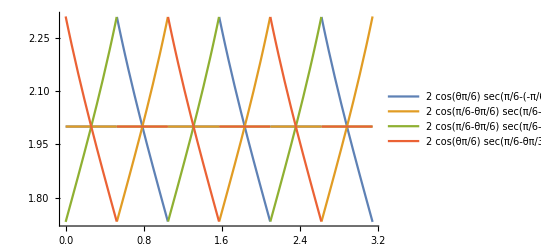

```mathematica
Plot[Evaluate[Se[0,Mod[θ,Pi/6],θ] ],{θ,0,Pi},PlotLegends->"Expressions"]
```

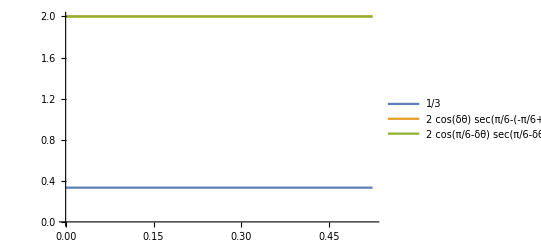

```mathematica
Plot[Evaluate[SS[0,δθ,θ][[1,1,1]] ],{δθ,0,Pi/6},PlotLegends->"Expressions"]
```

```mathematica
ApplyToPiecewise[approxSimplify,SS[n,δθ,θ]]
```

Piecewise[{{{1/3,2^(1-n),2^(1-n)}, 0≤Mod[θ,π]<π/6}, {{1/3,-2^(1-n),2^(1-n)}, π/6≤Mod[θ,π]<π/3}, {{1/3,-2^(1-n),-2^(1-n)}, π/3≤Mod[θ,π]<π/2}, {{1/3,2^(1-n),-2^(1-n)}, π/2≤Mod[θ,π]<(2 π)/3}, {{1/3,2^(1-n),2^(1-n)}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1/3,-2^(1-n),2^(1-n)}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
ApplyToPiecewise[approxSimplify,Piecewise[{{{1/3,Se[n,δθ,0Pi/6+δθ][[1]],Se[n,δθ,0Pi/6+δθ][[2]]}, 0≤Mod[θ,π]<π/6}, {{1/3,-Se[n,δθ,1Pi/6+δθ][[3]],Se[n,δθ,1Pi/6+δθ][[4]]}, π/6≤Mod[θ,π]<π/3}, {{1/3,-Se[n,δθ,2Pi/6+δθ][[1]],-Se[n,δθ,2Pi/6+δθ][[2]]}, π/3≤Mod[θ,π]<π/2}, {{1/3,Se[n,δθ,3Pi/6+δθ][[3]],-Se[n,δθ,3Pi/6+δθ][[4]]}, π/2≤Mod[θ,π]<(2 π)/3}, {{1/3,Se[n,δθ,4Pi/6+δθ][[1]],Se[n,δθ,4Pi/6+δθ][[2]]}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1/3,-Se[n,δθ,5Pi/6+δθ][[3]],Se[n,δθ,5Pi/6+δθ][[4]]}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]]
```

Piecewise[{{{1/3,2^(1-n),2^(1-n)}, 0≤Mod[θ,π]<π/6}, {{1/3,-2^(1-n),2^(1-n)}, π/6≤Mod[θ,π]<π/3}, {{1/3,-2^(1-n),-2^(1-n)}, π/3≤Mod[θ,π]<π/2}, {{1/3,2^(1-n),-2^(1-n)}, π/2≤Mod[θ,π]<(2 π)/3}, {{1/3,2^(1-n),2^(1-n)}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1/3,-2^(1-n),2^(1-n)}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
Plot[Evaluate[Se[0,Mod[θ,Pi/6],θ]],{θ,0,Pi},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
2^(1 - n)*(cos*δθ)*(sec*(Pi/6 - Mod[θ, Pi/3]))
```

```mathematica
2^(1-n) cos(δθ) sec(π/6-θπ/3)
```

```mathematica
scale["rR","ffR"]=Function[{θ,δθ},Piecewise[{{{1,Cos[δθ],Cos[π/6-δθ]}, 0≤Mod[θ,π]<π/6}, {{1,-Cos[π/6-δθ],Cos[δθ]}, π/6≤Mod[θ,π]<π/3}, {{1,-Cos[δθ],-Cos[π/6-δθ]}, π/3≤Mod[θ,π]<π/2}, {{1,Cos[π/6-δθ],-Cos[δθ]}, π/2≤Mod[θ,π]<(2 π)/3}, {{1,Cos[δθ],Cos[π/6-δθ]}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1,-Cos[π/6-δθ],Cos[δθ]}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]]
```

### Junk

```mathematica
InputForm[scale["rR","fR"][θ]]
```

Piecewise[{{{1, Cos[θ], Cos[Pi/6 - θ]}, Inequality[0, LessEqual, Mod[θ, 2*Pi], Less, Pi/6] || 
    Inequality[Pi, LessEqual, Mod[θ, 2*Pi], Less, (7*Pi)/6]}, {{1, -Sin[Pi/6 + θ], Cos[Pi/6 - θ]}, 
   Inequality[Pi/6, LessEqual, Mod[θ, 2*Pi], Less, Pi/3] || Inequality[(7*Pi)/6, LessEqual, Mod[θ, 2*Pi], Less, (4*Pi)/3]}, 
  {{1, -Sin[Pi/6 + θ], -Sin[θ]}, Inequality[Pi/3, LessEqual, Mod[θ, 2*Pi], Less, Pi/2] || 
    Inequality[(4*Pi)/3, LessEqual, Mod[θ, 2*Pi], Less, (3*Pi)/2]}, {{1, -Sin[Pi/6 - θ], -Sin[θ]}, 
   Inequality[Pi/2, LessEqual, Mod[θ, 2*Pi], Less, (2*Pi)/3] || Inequality[(3*Pi)/2, LessEqual, Mod[θ, 2*Pi], Less, 
     (5*Pi)/3]}, {{1, -Sin[Pi/6 - θ], -Cos[Pi/6 + θ]}, Inequality[(2*Pi)/3, LessEqual, Mod[θ, 2*Pi], Less, (5*Pi)/6] || 
    Inequality[(5*Pi)/3, LessEqual, Mod[θ, 2*Pi], Less, (11*Pi)/6]}, {{1, Cos[θ], -Cos[Pi/6 + θ]}, 
   Inequality[(5*Pi)/6, LessEqual, Mod[θ, 2*Pi], Less, Pi] || Inequality[(11*Pi)/6, LessEqual, Mod[θ, 2*Pi], Less, 2*Pi]}}, 0]

```mathematica
InputForm[fR[θ]]
```

Piecewise[{{{{1, 1, 1}, {-(Sec[θ]*Sin[Pi/6 + θ]), 1, -(Sec[θ]*Sin[Pi/6 - θ])}, 
    {-(Cos[Pi/6 + θ]*Sec[Pi/6 - θ]), -(Sec[Pi/6 - θ]*Sin[θ]), 1}}, Inequality[0, LessEqual, Mod[θ, 2*Pi], Less, Pi/6] || 
    Inequality[Pi, LessEqual, Mod[θ, 2*Pi], Less, (7*Pi)/6]}, 
  {{{1, 1, 1}, {1, -(Cos[θ]*Csc[Pi/6 + θ]), Csc[Pi/6 + θ]*Sin[Pi/6 - θ]}, {-(Cos[Pi/6 + θ]*Sec[Pi/6 - θ]), 
     -(Sec[Pi/6 - θ]*Sin[θ]), 1}}, Inequality[Pi/6, LessEqual, Mod[θ, 2*Pi], Less, Pi/3] || 
    Inequality[(7*Pi)/6, LessEqual, Mod[θ, 2*Pi], Less, (4*Pi)/3]}, 
  {{{1, 1, 1}, {1, -(Cos[θ]*Csc[Pi/6 + θ]), Csc[Pi/6 + θ]*Sin[Pi/6 - θ]}, {Cos[Pi/6 + θ]*Csc[θ], 1, 
     -(Cos[Pi/6 - θ]*Csc[θ])}}, Inequality[Pi/3, LessEqual, Mod[θ, 2*Pi], Less, Pi/2] || 
    Inequality[(4*Pi)/3, LessEqual, Mod[θ, 2*Pi], Less, (3*Pi)/2]}, 
  {{{1, 1, 1}, {Csc[Pi/6 - θ]*Sin[Pi/6 + θ], -(Cos[θ]*Csc[Pi/6 - θ]), 1}, {Cos[Pi/6 + θ]*Csc[θ], 1, 
     -(Cos[Pi/6 - θ]*Csc[θ])}}, Inequality[Pi/2, LessEqual, Mod[θ, 2*Pi], Less, (2*Pi)/3] || 
    Inequality[(3*Pi)/2, LessEqual, Mod[θ, 2*Pi], Less, (5*Pi)/3]}, 
  {{{1, 1, 1}, {Csc[Pi/6 - θ]*Sin[Pi/6 + θ], -(Cos[θ]*Csc[Pi/6 - θ]), 1}, {1, Sec[Pi/6 + θ]*Sin[θ], 
     -(Cos[Pi/6 - θ]*Sec[Pi/6 + θ])}}, Inequality[(2*Pi)/3, LessEqual, Mod[θ, 2*Pi], Less, (5*Pi)/6] || 
    Inequality[(5*Pi)/3, LessEqual, Mod[θ, 2*Pi], Less, (11*Pi)/6]}, 
  {{{1, 1, 1}, {-(Sec[θ]*Sin[Pi/6 + θ]), 1, -(Sec[θ]*Sin[Pi/6 - θ])}, {1, Sec[Pi/6 + θ]*Sin[θ], 
     -(Cos[Pi/6 - θ]*Sec[Pi/6 + θ])}}, Inequality[(5*Pi)/6, LessEqual, Mod[θ, 2*Pi], Less, Pi] || 
    Inequality[(11*Pi)/6, LessEqual, Mod[θ, 2*Pi], Less, 2*Pi]}}, 0]

rR[θ]=(1 | 1 | 1
-sin(θ+π/6) | cos(θ) | -sin(π/6-θ)
-cos(θ+π/6) | -sin(θ) | cos(π/6-θ))=(1 | 1 | 1
sin(θ-(5π)/6) | sin(θ+(3π)/6) | sin(θ-π/6)
sin(θ-(2 π)/6) | sin(θ-(6 π)/6) | sin(θ+(2π)/6))

Each row is a series of three sin waves each (2π)/3 out of phase with each other. The rows are π/2 out of phase with each other. Sin changes sign in steps of π. By examination a function which determines which element has a different sign can be written.
Let Θ = θπ/6
rR[θ]=(1 | 1 | 1
sin(Θ +((i-5)π)/6) | sin(Θ +((i+3)π)/6) | sin(Θ +((i-1)π)/6)
sin(Θ +((i-2) π)/6) | sin(Θ +((i-6) π)/6) | sin(Θ +((i+2)π)/6))   where    i=0,1,2,... 11
 (i-5)(i+3)(i-1)<0 then 1 negative 2 positive in 2nd Row.
(i-5)(i+3)(i-1)>0 then 2 negative 1 positive in 2nd Row.. 

       (i-2)(i-6)(i+2)<0 then 1 negative 2 positive in 3rd Row.
(i-2)(i-6)(i+2)>0 then 2 negative 1 positive in 3rd Row.

```mathematica
Reduce[(i-5)(i+3)(i-1)< 0&&i≥0&&i≤ 11&&Element[i,Integers]]
Reduce[(i-2)(i-6)(i+2)< 0&&i≥0&&i≤ 11&&Element[i,Integers]]
```

i==2||i==3||i==4

i==3||i==4||i==5

Let Θ = (6 θ)/π
rR[θ]=(1 | 1 | 1
sin(((Θ-5)π)/6) | sin(((Θ+3)π)/6) | sin(((Θ-1)π)/6)
sin(((Θ-2) π)/6) | sin(((Θ-6) π)/6) | sin(((Θ+2)π)/6))   where    0≤ Θ<12
 (Θ-5)(Θ+3)(Θ-1)<0 then 1 negative 2 positive in 2nd Row.
(Θ-5)(Θ+3)(Θ-1)>0 then 2 negative 1 positive in 2nd Row.. 

       (Θ-2)(Θ-6)(Θ+2)<0 then 1 negative 2 positive in 3rd Row.
(Θ-2)(Θ-6)(Θ+2)>0 then 2 negative 1 positive in 3rd Row.

```mathematica
Reduce[(Θ-5)(Θ+3)(Θ-1)< 0&&Θ≥0&&Θ< 12]
Reduce[(Θ-2)(Θ-6)(Θ+2)< 0&&Θ≥0&&Θ<12]
```

1<Mod[θ,π/6]<5

2<Mod[θ,π/6]<6

```mathematica
TraditionalForm[Θ = Mod[θ,Pi/6]]
```

θπ/6

Reduce[(i - 5) (i + 3) (i - 1) < 0 && i >= 0 && i <= 11 && Element[i, Integers]]
Reduce[(i - 2) (i - 6) (i + 2) < 0 && i >= 0 && i <= 11 && Element[i, Integers]]

Reduce[(i - 5) (i + 3) (i - 1) < 0 && i >= 0 && i <= 11 && Element[i, Integers]]
Reduce[(i - 2) (i - 6) (i + 2) < 0 && i >= 0 && i <= 11 && Element[i, Integers]]

```mathematica
Clear[cyclicSolve]
cyclicSolve[cond_,n_]:=Module[{hCond,evalQ},
If[TrueQ[HoldComplete[cond][[1,0]]==Inequality],
hCond = HoldComplete[cond][[1,0]][HoldComplete[cond][[1,1]]+ n*Pi,HoldComplete[cond][[1,2]],HoldComplete[cond][[1,3]],HoldComplete[cond][[1,4]],HoldComplete[cond][[1,5]]+ n*Pi];
evalQ = TrueQ[HoldComplete[cond][[1,3,0]]==Symbol],
hCond = HoldComplete[cond][[1,0]][HoldComplete[cond][[1,1]]+ n*Pi,HoldComplete[cond][[1,2]],HoldComplete[cond][[1,3]]+ n*Pi];
evalQ = TrueQ[HoldComplete[cond][[1,2,0]]==Symbol]];
If[evalQ,ReleaseHold[hCond],ReleaseHold[hCond]/.Flatten[FindInstance[ReleaseHold[hCond]&&n∈Integers,n]/.List[]->List[Rule[n,0]] ]]]

SetAttributes[cyclicSolve,HoldAllComplete]
```

```mathematica
inPiBySixRegion[θ_,ψ_]:=StringJoin[ToString[Floor[6 θ/Pi]Pi/6,TraditionalForm]," < ",ToString[ψ,TraditionalForm]," < ",ToString[(Floor[6 θ/Pi]+1)Pi/6,TraditionalForm ]]
inOnPiBySixRegion[θ_,ψ_]:=StringJoin[ToString[Floor[6 θ/Pi]Pi/6,TraditionalForm]," <= ",ToString[ψ,TraditionalForm]," < ",ToString[(Floor[6 θ/Pi]+1)Pi/6,TraditionalForm ]]
```

```mathematica
Clear[YABDiscretFactor];
YABDiscretFactor =Function[{θ,wrkRange,ψ},Evaluate[Piecewise[Table[{(  {1/3,2/wrkRange,2/wrkRange}  matSameSign[rR[ϕ]] Map[If[#≥1/2,1,0]&,Abs[rR[ϕ]],{2}] rR[θ]).{1,1,1},cSol[ToExpression[inOnPiBySixRegion[ϕ,ψ]],n]} ,{ϕ,Pi/12 ,Pi,Pi/6}],Null]]]/. cSol->cyclicSolve;
```

```mathematica
Clear[fYAB,ϕ,ψ]
fYAB =Function[{θ,wrkRange,ψ},Evaluate[Piecewise[Table[ {{1,wrkRange,wrkRange} rR[θ]/YABDiscretFactor[θ,1,ϕ],cSol[ToExpression[inOnPiBySixRegion[ϕ,ψ]],n]},{ϕ,Pi/12 ,Pi,Pi/6}],Null]]]/. cSol->cyclicSolve;
```

```mathematica
fR[θ_,rRange_:1]:=Piecewise[{{{{1, 1, 1}, rRange {1/2, -(Cos[θ]*Csc[Pi/6 + θ])/2, (Csc[Pi/6 + θ]*Sin[Pi/6 - θ])/2}, 
    rRange {1/2, (Sec[Pi/6 + θ]*Sin[θ])/2, -(Cos[Pi/6 - θ]*Sec[Pi/6 + θ])/2}}, Inequality[0, LessEqual, Mod[θ,Pi/2], Less, Pi/6 ]}, 
  {{{1, 1, 1}, rRange {-(Sec[θ]*Sin[Pi/6 + θ])/2, 1/2, -(Sec[θ]*Sin[Pi/6 - θ])/2}, rRange {(Cos[Pi/6 + θ]*Csc[θ])/2, 1/2, -(Cos[Pi/6 - θ]*Csc[θ])/2}}, 
   Inequality[Pi/6 , LessEqual, Mod[θ,Pi/2], Less, Pi/3 ]}, {{{1, 1, 1}, rRange {(Csc[Pi/6 - θ]*Sin[Pi/6 + θ])/2, -(Cos[θ]*Csc[Pi/6 - θ])/2, 1/2}, 
    rRange {-(Cos[Pi/6 + θ]*Sec[Pi/6 - θ])/2, -(Sec[Pi/6 - θ]*Sin[θ])/2, 1/2}}, Inequality[Pi/3 , LessEqual, Mod[θ,Pi/2], Less, Pi/2 ]}}, Null]
```

```mathematica
fRScale[θ_,rRange_]:=Piecewise[{{{1, -((2*Sin[Pi/6 + θ])/rRange), -((2*Cos[Pi/6 + θ])/rRange)}, Inequality[0, LessEqual, Mod[θ,Pi/2], Less, Pi/6 ]}, 
   {{1, (2*Cos[θ])/rRange, -((2*Sin[θ])/rRange)}, Inequality[Pi/6 , LessEqual, Mod[θ,Pi/2], Less, Pi/3 ]}, 
   {{1, -((2*Sin[Pi/6 - θ])/rRange), (2*Cos[Pi/6 - θ])/rRange}, Inequality[Pi/3 , LessEqual, Mod[θ,Pi/2], Less, Pi/2 ]}}, Null]
```

```mathematica
qR[θ_,n_:8]:=Piecewise[{{{{1,1,1},{IntegerPart[2^(-2+n)],-IntegerPart[2^(-2+n)*Cos[θ]*Csc[Pi/6+θ]],IntegerPart[2^(-2+n)*Csc[Pi/6+θ]*Sin[Pi/6-θ]]},{IntegerPart[2^(-2+n)],IntegerPart[2^(-2+n)*Sec[Pi/6+θ]*Sin[θ]],-IntegerPart[2^(-2+n)*Cos[Pi/6-θ]*Sec[Pi/6+θ]]}},Inequality[0,LessEqual,Mod[θ,Pi/2],Less,Pi/6]},{{{1,1,1},{-IntegerPart[2^(-2+n)*Sec[θ]*Sin[Pi/6+θ]],IntegerPart[2^(-2+n)],-IntegerPart[2^(-2+n)*Sec[θ]*Sin[Pi/6-θ]]},{IntegerPart[2^(-2+n)*Cos[Pi/6+θ]*Csc[θ]],IntegerPart[2^(-2+n)],-IntegerPart[2^(-2+n)*Cos[Pi/6-θ]*Csc[θ]]}},Inequality[Pi/6,LessEqual,Mod[θ,Pi/2],Less,Pi/3]},{{{1,1,1},{IntegerPart[2^(-2+n)*Csc[Pi/6-θ]*Sin[Pi/6+θ]],-IntegerPart[2^(-2+n)*Cos[θ]*Csc[Pi/6-θ]],IntegerPart[2^(-2+n)]},{-IntegerPart[2^(-2+n)*Cos[Pi/6+θ]*Sec[Pi/6-θ]],-IntegerPart[2^(-2+n)*Sec[Pi/6-θ]*Sin[θ]],IntegerPart[2^(-2+n)]}},Inequality[Pi/3,LessEqual,Mod[θ,Pi/2],Less,Pi/2]}},Null]
```

```mathematica
qRScale[θ_,n_:8]:=Piecewise[{{{1,-(2^(2-n)*Sin[Pi/6+θ]),-(2^(2-n)*Cos[Pi/6+θ])},Inequality[0,LessEqual,Mod[θ,Pi/2],Less,Pi/6]},{{1,2^(2-n)*Cos[θ],-(2^(2-n)*Sin[θ])},Inequality[Pi/6,LessEqual,Mod[θ,Pi/2],Less,Pi/3]},{{1,-(2^(2-n)*Sin[Pi/6-θ]),2^(2-n)*Cos[Pi/6-θ]},Inequality[Pi/3,LessEqual,Mod[θ,Pi/2],Less,Pi/2]}},Null]
```

```mathematica
Clear[n,factor,mat,error,pts,iRot,rot,ptsError];
approxReport[θ_,n_]:=Block[{mat,error,ptsError,Rstr,qRstr,errorstr,minMaxerrorstr,thetastr},
mat =  qR[θ,n];
error = qRScale[θ,n]  mat- N[rR[θ]];
ptsError = 2^n error . RGBCube[RGB];
Rstr = StringJoin["R[",ToString[θ,TraditionalForm],"] = ",mForm[colorMat[rR[θ]]]];
qRstr = StringJoin["qR[",ToString[θ,TraditionalForm],", ",ToString[n,TraditionalForm]," bit] = ",mForm[colorMat[qR[θ,n]]]];
qRScalestr = StringJoin["qRScale[",ToString[θ,TraditionalForm],", ",ToString[n,TraditionalForm]," bit] = ",mForm[colorMat[qRScale[θ,n]]]];
verbErrorstr = StringJoin[mForm[qRScale[θ,n]] ,"⊗", mForm[ mat]," - ",mForm[rR[θ]]," = ",mForm[error]];
errorstr = StringJoin["qRScale ⊗ qR - R = ",mForm[error]];
minMaxerrorstr = StringJoin["minMaxError = ",mForm[Map[{Min[#],Max[#]}&,Threshold[ptsError],1]]];
thetastr = StringJoin["θ = ",ToString[θ,TraditionalForm]];
Panel[Grid[{{Column[{Rstr,
qRstr,qRScalestr}],Column[{Framed[errorstr],minMaxerrorstr}]}}],{thetastr},{Top}]]
```

```mathematica
Piecewise[{
{Subscript[fR, a], Or @@ Table[Inequality[       0 + (i*Pi)/2, LessEqual, θ, Less, (1/6)*Pi + (i*Pi)/2], {i, 0, 3}]}, 
   {Subscript[fR, b], Or @@ Table[Inequality[(1/6)*Pi + (i*Pi)/2, LessEqual, θ, Less, (1/3)*Pi + (i*Pi)/2], {i, 0, 3}]}, 
   {Subscript[fR, c], Or @@ Table[Inequality[(1/3)*Pi + (i*Pi)/2, LessEqual, θ, Less, (1/2)*Pi + (i*Pi)/2], {i, 0, 3}]}}, Null]
```

Piecewise[{{fR_a, 0≤θ<π/6||π/2≤θ<(2 π)/3||π≤θ<(7 π)/6||(3 π)/2≤θ<(5 π)/3}, {fR_b, π/6≤θ<π/3||(2 π)/3≤θ<(5 π)/6||(7 π)/6≤θ<(4 π)/3||(5 π)/3≤θ<(11 π)/6}, {fR_c, π/3≤θ<π/2||(5 π)/6≤θ<π||(4 π)/3≤θ<(3 π)/2||(11 π)/6≤θ<2 π}, {Null, True}}]

```mathematica
Row[{
partShow[Piecewise[{
{Subscript[fR, a], Or @@ Table[Inequality[       0 + (i*Pi)/2, LessEqual, θ, Less, (1/6)*Pi + (i*Pi)/2], {i, 0, 3}]}, 
   {Subscript[fR, b], Or @@ Table[Inequality[(1/6)*Pi + (i*Pi)/2, LessEqual, θ, Less, (1/3)*Pi + (i*Pi)/2], {i, 0, 3}]}, 
   {Subscript[fR, c], Or @@ Table[Inequality[(1/3)*Pi + (i*Pi)/2, LessEqual, θ, Less, (1/2)*Pi + (i*Pi)/2], {i, 0, 3}]}}, Null]],
Column[{
Row[{Subscript[fR,a]," = ",TraditionalForm[fR[θ][[1,1,1]]]}],
Row[{Subscript[fR,b]," = ",TraditionalForm[fR[θ][[1,2,1]]]}],
Row[{Subscript[fR,c]," = ",TraditionalForm[fR[θ][[1,3,1]]]}]}]}]
```

```mathematica
-Graphics-{{Subscript[fR, a]" = "({{1, 1, 1}, {1, -cos(θ) csc(θ+π/6), csc(θ+π/6) sin(π/6-θ)}, {1, sec(θ+π/6) sin(θ), -cos(π/6-θ) sec(θ+π/6)}})}, {Subscript[fR, b]" = "({{1, 1, 1}, {-sec(θ) sin(θ+π/6), 1, -sec(θ) sin(π/6-θ)}, {cos(θ+π/6) csc(θ), 1, -cos(π/6-θ) csc(θ)}})}, {Subscript[fR, c]" = "({{1, 1, 1}, {csc(π/6-θ) sin(θ+π/6), -cos(θ) csc(π/6-θ), 1}, {-cos(θ+π/6) sec(π/6-θ), -sec(π/6-θ) sin(θ), 1}})}}
```

```mathematica
Manipulate[
ϕ=nearestMin[θ,errorMinsOneTable[[n-1]]][[1]];
ψ=nearestMin[θ,errorMinsHalfTable[[n-1]]][[1]];
Column[{approxReport[θ,n],approxReport[ϕ,n],approxReport[ψ,n]}],{θ,-Pi,Pi},{{n,8},2,32,1}]
```

Part::partd: Part specification errorMinsOneTable ⟦ 7 ⟧ is longer than depth of object.

Part::partd: Part specification errorMinsHalfTable ⟦ 7 ⟧ is longer than depth of object.

Part::partd: Part specification errorMinsOneTable ⟦ 7 ⟧ is longer than depth of object.

Part::partd: Part specification errorMinsHalfTable ⟦ 7 ⟧ is longer than depth of object.

MapAt::partw: Part {2, 2, 2, 1, 2, 3} of qRScale[0.389557, 8] does not exist.

Threshold::wlist: Argument 256\ {{-1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8]}, {0.791437  + 64\ qRScale[0.389557, 8], -0.925077 - « 1 », 0.13364  + 10\ qRScale[0.389557, 8]}, {0.611251  + 64\ qRScale[0.389557, 8], 0.379779  + 39\ qRScale[0.389557, 8], -0.99103 - 103\ qRScale[0.389557, 8]}} . « 1 » should be one of rectangular array of any depth, image, sound, or sampled sound list.

Threshold::nlist: Argument {256\ {{-1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8]}, {0.791437  + 64\ qRScale[« 2 »], -0.925077 - 74\ qRScale[« 2 »], 0.13364  + 10\ qRScale[« 2 »]}, {0.611251  + 64\ qRScale[« 2 »], 0.379779  + 39\ qRScale[« 2 »], -0.99103 - 103\ qRScale[« 2 »]}} . RGBCube[RGB], 256\ {« 1 »} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

MapAt::partw: Part {2, 2, 2, 1, 2, 3} of qRScale[0.389557, 8] does not exist.

Threshold::wlist: Argument 256\ {{-1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8]}, {0.791437  + 64\ qRScale[0.389557, 8], -0.925077 - « 1 », 0.13364  + 10\ qRScale[0.389557, 8]}, {0.611251  + 64\ qRScale[0.389557, 8], 0.379779  + 39\ qRScale[0.389557, 8], -0.99103 - 103\ qRScale[0.389557, 8]}} . « 1 » should be one of rectangular array of any depth, image, sound, or sampled sound list.

Threshold::nlist: Argument {256\ {{-1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8]}, {0.791437  + 64\ qRScale[« 2 »], -0.925077 - 74\ qRScale[« 2 »], 0.13364  + 10\ qRScale[« 2 »]}, {0.611251  + 64\ qRScale[« 2 »], 0.379779  + 39\ qRScale[« 2 »], -0.99103 - 103\ qRScale[« 2 »]}} . RGBCube[RGB], 256\ {« 1 »} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

MapAt::partw: Part {2, 2, 2, 1, 2, 3} of qRScale[0.389557, 8] does not exist.

General::stop: Further output of MapAt :: partw will be suppressed during this calculation.

Threshold::wlist: Argument 256\ {{-1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8]}, {0.791437  + 64\ qRScale[0.389557, 8], -0.925077 - « 1 », 0.13364  + 10\ qRScale[0.389557, 8]}, {0.611251  + 64\ qRScale[0.389557, 8], 0.379779  + 39\ qRScale[0.389557, 8], -0.99103 - 103\ qRScale[0.389557, 8]}} . « 1 » should be one of rectangular array of any depth, image, sound, or sampled sound list.

General::stop: Further output of Threshold :: wlist will be suppressed during this calculation.

Threshold::nlist: Argument {256\ {{-1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8], -1. + qRScale[0.389557, 8]}, {0.791437  + 64\ qRScale[« 2 »], -0.925077 - 74\ qRScale[« 2 »], 0.13364  + 10\ qRScale[« 2 »]}, {0.611251  + 64\ qRScale[« 2 »], 0.379779  + 39\ qRScale[« 2 »], -0.99103 - 103\ qRScale[« 2 »]}} . RGBCube[RGB], 256\ {« 1 »} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Threshold :: nlist will be suppressed during this calculation.

Part::partd: Part specification errorMinsOneTable ⟦ 7 ⟧ is longer than depth of object.

Part::partd: Part specification errorMinsHalfTable ⟦ 7 ⟧ is longer than depth of object.

Threshold::wlist: Argument 256\ {{0., 0., 0.}, {0., -0.00997824, 0.00997824}, {0., 0.00729813, -0.00729813}} . RGBCube[RGB] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Threshold::nlist: Argument {256\ {{0., 0., 0.}, {0., -0.00997824, 0.00997824}, {0., 0.00729813, -0.00729813}} . RGBCube[RGB], 256\ {{0., 0., 0.}, {0., -0.00997824, 0.00997824}, {0., 0.00729813, -0.00729813}} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

Threshold::wlist: Argument 256\ {{0., 0., 0.}, {0., -0.00997824, 0.00997824}, {0., 0.00729813, -0.00729813}} . RGBCube[RGB] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Threshold::nlist: Argument {256\ {{0., 0., 0.}, {0., -0.00997824, 0.00997824}, {0., 0.00729813, -0.00729813}} . RGBCube[RGB], 256\ {{0., 0., 0.}, {0., -0.00997824, 0.00997824}, {0., 0.00729813, -0.00729813}} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

Threshold::wlist: Argument 256\ {{0., 0., 0.}, {0., -0.00997824, 0.00997824}, {0., 0.00729813, -0.00729813}} . RGBCube[RGB] should be one of rectangular array of any depth, image, sound, or sampled sound list.

General::stop: Further output of Threshold :: wlist will be suppressed during this calculation.

Threshold::nlist: Argument {256\ {{0., 0., 0.}, {0., -0.00997824, 0.00997824}, {0., 0.00729813, -0.00729813}} . RGBCube[RGB], 256\ {{0., 0., 0.}, {0., -0.00997824, 0.00997824}, {0., 0.00729813, -0.00729813}} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Threshold :: nlist will be suppressed during this calculation.

Part::partd: Part specification errorMinsOneTable ⟦ 7 ⟧ is longer than depth of object.

Part::partd: Part specification errorMinsHalfTable ⟦ 7 ⟧ is longer than depth of object.

Threshold::wlist: Argument 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Threshold::nlist: Argument {256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB], 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

Threshold::wlist: Argument 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Threshold::nlist: Argument {256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB], 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

Threshold::wlist: Argument 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB] should be one of rectangular array of any depth, image, sound, or sampled sound list.

General::stop: Further output of Threshold :: wlist will be suppressed during this calculation.

Threshold::nlist: Argument {256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB], 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Threshold :: nlist will be suppressed during this calculation.

Part::partd: Part specification errorMinsOneTable ⟦ 7 ⟧ is longer than depth of object.

Part::partd: Part specification errorMinsHalfTable ⟦ 7 ⟧ is longer than depth of object.

Threshold::wlist: Argument 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Threshold::nlist: Argument {256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB], 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

Threshold::wlist: Argument 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Threshold::nlist: Argument {256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB], 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

Threshold::wlist: Argument 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB] should be one of rectangular array of any depth, image, sound, or sampled sound list.

General::stop: Further output of Threshold :: wlist will be suppressed during this calculation.

Threshold::nlist: Argument {256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB], 256\ {{0., 0., 0.}, {1.47158, -1.71651, 0.244936}, {0.983732, 0.618549, -1.60228}} . RGBCube[RGB]} is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Threshold :: nlist will be suppressed during this calculation.

Part::partd: Part specification errorMinsOneTable ⟦ 7 ⟧ is longer than depth of object.

Part::partd: Part specification errorMinsHalfTable ⟦ 7 ⟧ is longer than depth of object.

```mathematica
mat = fYAB[θ,1,θ];
factor=YABDiscretFactor[θ,rRange,θ];
TableForm[Table[{MatrixForm[factor[[1,i,1]]]⊗ int[MatrixForm[{1,rRange,rRange}] ⊗ MatrixForm[mat[[1,i,1]]]],mat[[1,i,2]]},{i,1,6}]]
```

```mathematica
mat = fR[θ,2];
factor=fRScale[θ,rRange];
TableForm[Table[{MatrixForm[factor[[1,i,1]]]⊗ int[MatrixForm[{1,rRange,rRange}] ⊗ MatrixForm[mat[[1,i,1]]]],mat[[1,i,2]]},{i,1,3}]]
```

(1
-(2 Sin[π/6+θ])/rRange
-(2 Cos[π/6+θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
1 | -Cos[θ] Csc[π/6+θ] | Csc[π/6+θ] Sin[π/6-θ]
1 | Sec[π/6+θ] Sin[θ] | -Cos[π/6-θ] Sec[π/6+θ])] | 0≤Mod[θ,π/2]<π/6
(1
(2 Cos[θ])/rRange
-(2 Sin[θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
-Sec[θ] Sin[π/6+θ] | 1 | -Sec[θ] Sin[π/6-θ]
Cos[π/6+θ] Csc[θ] | 1 | -Cos[π/6-θ] Csc[θ])] | π/6≤Mod[θ,π/2]<π/3
(1
-(2 Sin[π/6-θ])/rRange
(2 Cos[π/6-θ])/rRange)⊗int[(1
rRange
rRange)⊗(1 | 1 | 1
Csc[π/6-θ] Sin[π/6+θ] | -Cos[θ] Csc[π/6-θ] | 1
-Cos[π/6+θ] Sec[π/6-θ] | -Sec[π/6-θ] Sin[θ] | 1)] | π/3≤Mod[θ,π/2]<π/2